We have developed a Mathematica program package SpaceGroupIrep (https : // github.com/goodluck1982/SpaceGroupIrep) which is a database and tool set for irreducible representations (IRs) of space group in BC convention, i.e.the convention used in the famous book “The mathematical theory of symmetry in solids”.94 by C.J.Bradley & A.P.Cracknell (called the BC book afterwards).Using this package, elements of any space group, little group, Herring little group, or central extension of little cogroup can be easily obtained.This package can give not only little-group (LG) IRs for any k-point but also space-group (SG) IRs for any k-stars in intuitive table form, and both single-valued and double-valued IRs are supported.This package can calculate the decomposition of the direct product of SG IRs for any two k-stars.This package can determine the LG IRs of Bloch states in energy bands in BC convention and this works for any input primitive cell thanks to its ability to convert any input cell to a cell in BC convention.This package can also provide the correspondence of k-points and LG IR labels between BCS (Bilbao Crystallographic Server) and BC conventions.In a word, the package SpaceGroupIrep is very useful for both study and research, e.g.for analyzing band topology or determining selection rules in physics.

For details of the package, please refer to the paper arXiv:2012.08871 (https : // arxiv.org/abs/2012.08871).

After the SpaceGroupIrep package is installed, using the following code to enable it.

```mathematica
<<"SpaceGroupIrep`"
```

Examples to demonstrate the functions of the package are given in the  following contents.

## 1. Bravais lattice and Brillouin zone

### The 14 Bravais lattices

To describe space group, Bravais lattice is needed. As we know, there are 14 Bravais lattices in total in 3D space. In this package, we use a string to represent a certain Bravais lattice. All available strings are shown as following.

```mathematica
BravLatt//Values//InputForm
```

{"TricPrim", "MonoPrim", "MonoBase", "OrthPrim", "OrthBase", "OrthBody", "OrthFace", "TetrPrim", 
 "TetrBody", "TrigPrim", "HexaPrim", "CubiPrim", "CubiFace", "CubiBody"}

### The 22 available Brillouin zone (BZ) type

Depending on the ratios of lattice constants, the shape of BZ may be different for certain Bravais lattice. There are five multiple-BZ Bravais lattice: “OrthBase”, “OrthBody”, “OrthFace”, “TetrBody”, “TrigPrim”. Therefore, there are 22 different types of BZ in total. The full strings to describe the BZ types are shown as following.  In some functions, only “a”, “b”, “c”, “d” are needed to designate the type of BZ in short, or a null string “” is used for the Bravais lattice with only one type of BZ.  Note that, following the convention used in the BC book,  reciprocal primitive cell, i.e. a parallelepiped centered at k = 0, is used as the (first) BZ of triclinic and monoclinic lattices, and  the Wigner-Seitz unit cell in reciprocal space is used as the BZ for other lattices.

```mathematica
bztypes=Keys[BCHighSymKpt];
InputForm[%]
```

{"TricPrim", "MonoPrim", "MonoBase", "OrthPrim", "OrthBase(a)", "OrthBase(b)", "OrthBody(a)", 
 "OrthBody(b)", "OrthBody(c)", "OrthFace(a)", "OrthFace(b)", "OrthFace(c)", "OrthFace(d)", 
 "TetrPrim", "TetrBody(a)", "TetrBody(b)", "TrigPrim(a)", "TrigPrim(b)", "HexaPrim", "CubiPrim", 
 "CubiFace", "CubiBody"}

### The basic vectors of the given Bravais lattice

The BC book uses certain basic vectors for certain Bravais lattice as defined in the BC-Tab. 3.1 (BC-Tab. 3.1 means the Tab. 3.1 in the BC book). All the SG elements used in the BC book are defined using these basic vectors.  There are 14 sets of basic vectors used in the BC book, each set  of basic vectors for each Bravais lattice.

```mathematica
BasicVectors["OrthBody"]    (* give the basic vectors of "OrthBody" lattice *)
vec=%/.{a->1,b->2,c->3}
checkBasVec["OrthBody",vec]  (* check whether vec belongs to "OrthBody" lattice and gives its type if true *)
```

{{a/2,b/2,c/2},{-a/2,-b/2,c/2},{a/2,-b/2,-c/2}}

{{1/2,1,3/2},{-1/2,-1,3/2},{1/2,-1,-3/2}}

{True,c,{a→1,b→2,c→3}}

Users can take advantage of  “?”  to see the short description of the usage or illustration of a function in SpaceGroupIrep. e.g.

```mathematica
?BasicVectors
```

An association from Bravais lattices to their basic vectors defined in Tab 3.1 of the BC book.

```mathematica
?checkBasVec
```

checkBasVec[brav,basvec] checks whether basvec is the basic vectors of the form in BC Tab.3.1. It also calculates the BZ type. The return value is a list of the form {True,"a",{a->2,c->3}}

### Show the rotatable Brillouin zone and high-symmetry (HS) k-points and k-lines

showBZDemo can be used to show a specific type of BZ.

```mathematica
showBZDemo["OrthBody(c)"]  (*using the basic vectors with default lattice constants*)
```

OrthBody(c)

{{Γ,{0,0,0}},{X,{1/2,1/2,-1/2}},{R,{1/2,0,0}},{S,{1/2,0,-1/2}},{T,{1/2,-1/2,0}},{W,{3/4,-1/4,-1/4}}}

{{Λ(ΓX),{u,u,-u}},{F(XF),{1/2+u,1/2-u,-1/2+u}},{P(TW),{1/2+u,-1/2+u,-u}},{Σ(ΓΣ),{u,-u,u}},{D(SW),{1/2+u,-u,-1/2+u}},{Δ(ΓΔ),{u,-u,-u}},{U(XU),{1/2+u,1/2-u,-1/2-u}},{Q(RW),{1/2+u,-u,-u}}}

F(XF): {1/2+u,1/2-u,-1/2+u}, u range is [0,0.1875]

Σ(ΓΣ): {u,-u,u}, u range is [0,0.3125]

Δ(ΓΔ): {u,-u,-u}, u range is [0,0.390625]

U(XU): {1/2+u,1/2-u,-1/2-u}, u range is [0,0.109375]

-Graphics3D-

```mathematica
showBZDemo["OrthBody(c)",vec]  (*using the user-specified basic vectors*)
```

OrthBody(c)

{{Γ,{0,0,0}},{X,{1/2,1/2,-1/2}},{R,{1/2,0,0}},{S,{1/2,0,-1/2}},{T,{1/2,-1/2,0}},{W,{3/4,-1/4,-1/4}}}

{{Λ(ΓX),{u,u,-u}},{F(XF),{1/2+u,1/2-u,-1/2+u}},{P(TW),{1/2+u,-1/2+u,-u}},{Σ(ΓΣ),{u,-u,u}},{D(SW),{1/2+u,-u,-1/2+u}},{Δ(ΓΔ),{u,-u,-u}},{U(XU),{1/2+u,1/2-u,-1/2-u}},{Q(RW),{1/2+u,-u,-u}}}

F(XF): {1/2+u,1/2-u,-1/2+u}, u range is [0,0.222222]

Σ(ΓΣ): {u,-u,u}, u range is [0,0.277778]

Δ(ΓΔ): {u,-u,-u}, u range is [0,0.361111]

U(XU): {1/2+u,1/2-u,-1/2-u}, u range is [0,0.138889]

-Graphics3D-

## 2. Group elements and multiplication

### Rotation operations

Rotation matrices are defined under each Bravais lattice, therefore the same rotation may have different matrices for different Bravais lattices. To get the relations between the rotation name and rotation matrix, Bravais lattice has to be designated first. In addition, the rotation matrix in reciprocal space (or k-space) (Rk) is different from that in real space (Rr). The two matrices has the relation Rk=(Rrᵀ)^-1.

#### Rotation matrices

```mathematica
RotMat[[1]]["TrigPrim"]    (*all the available rotation names for "TrigPrim" lattice*)
getRotMat["TrigPrim",#]&/@%   (*get rotation matrices from their names*)
getRotName["TrigPrim",#]&/@%  (*get rotation names from their matrices*)
getRotMatOfK["TrigPrim",#]&/@%  (*get the k-space rotation matrices from their names*)
Inverse[#[[1]]ᵀ]==#[[2]]&/@Transpose[{%,%%%}] (*verify the realtions of Rk and Rr*)
```

{E,C3+,C3-,C21p,C22p,C23p,I,S6-,S6+,σd1,σd2,σd3}

{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,-1}},{{0,0,-1},{-1,0,0},{0,-1,0}},{{0,-1,0},{0,0,-1},{-1,0,0}},{{1,0,0},{0,0,1},{0,1,0}},{{0,0,1},{0,1,0},{1,0,0}},{{0,1,0},{1,0,0},{0,0,1}}}

{E,C3+,C3-,C21p,C22p,C23p,I,S6-,S6+,σd1,σd2,σd3}

{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,-1}},{{0,0,-1},{-1,0,0},{0,-1,0}},{{0,-1,0},{0,0,-1},{-1,0,0}},{{1,0,0},{0,0,1},{0,1,0}},{{0,0,1},{0,1,0},{1,0,0}},{{0,1,0},{1,0,0},{0,0,1}}}

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Examples for primitive cubic Bravais lattice.*)
RotMat[[1]]["CubiPrim"]
getRotMat["CubiPrim",#]&/@%
getRotName["CubiPrim",#]&/@%
getRotMatOfK["CubiPrim",#]&/@%
Inverse[#[[1]]ᵀ]==#[[2]]&/@Transpose[{%,%%%}]
```

{E,C2x,C2y,C2z,C31+,C32+,C33+,C34+,C31-,C32-,C33-,C34-,C4x+,C4y+,C4z+,C4x-,C4y-,C4z-,C2a,C2b,C2c,C2d,C2e,C2f,I,σx,σy,σz,S61-,S62-,S63-,S64-,S61+,S62+,S63+,S64+,S4x-,S4y-,S4z-,S4x+,S4y+,S4z+,σda,σdb,σdc,σdd,σde,σdf}

{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,-1,0}},{{0,0,-1},{-1,0,0},{0,1,0}},{{0,0,1},{-1,0,0},{0,-1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,1},{-1,0,0}},{{0,-1,0},{0,0,-1},{1,0,0}},{{1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{0,0,1},{0,-1,0},{1,0,0}},{{-1,0,0},{0,0,1},{0,1,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{-1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,-1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,-1}},{{0,0,-1},{-1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,1,0}},{{0,0,1},{1,0,0},{0,-1,0}},{{0,0,-1},{1,0,0},{0,1,0}},{{0,-1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{1,0,0}},{{0,1,0},{0,0,1},{-1,0,0}},{{-1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,-1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,-1}},{{-1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,-1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,-1},{0,1,0},{-1,0,0}},{{1,0,0},{0,0,-1},{0,-1,0}},{{0,0,1},{0,1,0},{1,0,0}},{{1,0,0},{0,0,1},{0,1,0}}}

{E,C2x,C2y,C2z,C31+,C32+,C33+,C34+,C31-,C32-,C33-,C34-,C4x+,C4y+,C4z+,C4x-,C4y-,C4z-,C2a,C2b,C2c,C2d,C2e,C2f,I,σx,σy,σz,S61-,S62-,S63-,S64-,S61+,S62+,S63+,S64+,S4x-,S4y-,S4z-,S4x+,S4y+,S4z+,σda,σdb,σdc,σdd,σde,σdf}

{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,-1}},{{-1,0,0},{0,-1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},{{0,0,-1},{1,0,0},{0,-1,0}},{{0,0,-1},{-1,0,0},{0,1,0}},{{0,0,1},{-1,0,0},{0,-1,0}},{{0,1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,1},{-1,0,0}},{{0,-1,0},{0,0,-1},{1,0,0}},{{1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,1}},{{1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,-1}},{{0,0,1},{0,-1,0},{1,0,0}},{{-1,0,0},{0,0,1},{0,1,0}},{{0,0,-1},{0,-1,0},{-1,0,0}},{{-1,0,0},{0,0,-1},{0,-1,0}},{{-1,0,0},{0,-1,0},{0,0,-1}},{{-1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,-1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,-1}},{{0,0,-1},{-1,0,0},{0,-1,0}},{{0,0,1},{-1,0,0},{0,1,0}},{{0,0,1},{1,0,0},{0,-1,0}},{{0,0,-1},{1,0,0},{0,1,0}},{{0,-1,0},{0,0,-1},{-1,0,0}},{{0,-1,0},{0,0,1},{1,0,0}},{{0,1,0},{0,0,-1},{1,0,0}},{{0,1,0},{0,0,1},{-1,0,0}},{{-1,0,0},{0,0,1},{0,-1,0}},{{0,0,-1},{0,-1,0},{1,0,0}},{{0,1,0},{-1,0,0},{0,0,-1}},{{-1,0,0},{0,0,-1},{0,1,0}},{{0,0,1},{0,-1,0},{-1,0,0}},{{0,-1,0},{1,0,0},{0,0,-1}},{{0,-1,0},{-1,0,0},{0,0,1}},{{0,1,0},{1,0,0},{0,0,1}},{{0,0,-1},{0,1,0},{-1,0,0}},{{1,0,0},{0,0,-1},{0,-1,0}},{{0,0,1},{0,1,0},{1,0,0}},{{1,0,0},{0,0,1},{0,1,0}}}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Check the rotation matrices. The results should be the same as BC-Tab. 3.2 *)
checkRotMat[BravLatt[#]]&/@Range[1,14]
```

{TricPrim
E | t1 | t2 | t3
I | -t1 | -t2 | -t3,MonoPrim
E | t1 | t2 | t3
C2z | -t1 | -t2 | t3
I | -t1 | -t2 | -t3
σz | t1 | t2 | -t3,MonoBase
E | t1 | t2 | t3
C2z | -t1 | -t3 | -t2
I | -t1 | -t2 | -t3
σz | t1 | t3 | t2,OrthPrim
E | t1 | t2 | t3
C2x | -t1 | t2 | -t3
C2y | t1 | -t2 | -t3
C2z | -t1 | -t2 | t3
I | -t1 | -t2 | -t3
σx | t1 | -t2 | t3
σy | -t1 | t2 | t3
σz | t1 | t2 | -t3,OrthBase
E | t1 | t2 | t3
C2x | t2 | t1 | -t3
C2y | -t2 | -t1 | -t3
C2z | -t1 | -t2 | t3
I | -t1 | -t2 | -t3
σx | -t2 | -t1 | t3
σy | t2 | t1 | t3
σz | t1 | t2 | -t3,OrthBody
E | t1 | t2 | t3
C2x | t3 | -t1-t2-t3 | t1
C2y | -t1-t2-t3 | t3 | t2
C2z | t2 | t1 | -t1-t2-t3
I | -t1 | -t2 | -t3
σx | -t3 | t1+t2+t3 | -t1
σy | t1+t2+t3 | -t3 | -t2
σz | -t2 | -t1 | t1+t2+t3,OrthFace
E | t1 | t2 | t3
C2x | -t2+t3 | -t2 | t1-t2
C2y | -t1 | -t1+t3 | -t1+t2
C2z | t2-t3 | t1-t3 | -t3
I | -t1 | -t2 | -t3
σx | t2-t3 | t2 | -t1+t2
σy | t1 | t1-t3 | t1-t2
σz | -t2+t3 | -t1+t3 | t3,TetrPrim
E | t1 | t2 | t3
C4z+ | t2 | -t1 | t3
C2z | -t1 | -t2 | t3
C4z- | -t2 | t1 | t3
C2x | t1 | -t2 | -t3
C2y | -t1 | t2 | -t3
C2a | t2 | t1 | -t3
C2b | -t2 | -t1 | -t3
I | -t1 | -t2 | -t3
S4z- | -t2 | t1 | -t3
σz | t1 | t2 | -t3
S4z+ | t2 | -t1 | -t3
σx | -t1 | t2 | t3
σy | t1 | -t2 | t3
σda | -t2 | -t1 | t3
σdb | t2 | t1 | t3,TetrBody
E | t1 | t2 | t3
C4z+ | -t3 | t1+t2+t3 | -t2
C2z | t2 | t1 | -t1-t2-t3
C4z- | t1+t2+t3 | -t3 | -t1
C2x | -t1-t2-t3 | t3 | t2
C2y | t3 | -t1-t2-t3 | t1
C2a | -t1 | -t2 | t1+t2+t3
C2b | -t2 | -t1 | -t3
I | -t1 | -t2 | -t3
S4z- | t3 | -t1-t2-t3 | t2
σz | -t2 | -t1 | t1+t2+t3
S4z+ | -t1-t2-t3 | t3 | t1
σx | t1+t2+t3 | -t3 | -t2
σy | -t3 | t1+t2+t3 | -t1
σda | t1 | t2 | -t1-t2-t3
σdb | t2 | t1 | t3,TrigPrim
E | t1 | t2 | t3
C3+ | t2 | t3 | t1
C3- | t3 | t1 | t2
C21p | -t1 | -t3 | -t2
C22p | -t3 | -t2 | -t1
C23p | -t2 | -t1 | -t3
I | -t1 | -t2 | -t3
S6- | -t2 | -t3 | -t1
S6+ | -t3 | -t1 | -t2
σd1 | t1 | t3 | t2
σd2 | t3 | t2 | t1
σd3 | t2 | t1 | t3,HexaPrim
E | t1 | t2 | t3
C6+ | t1+t2 | -t1 | t3
C3+ | t2 | -t1-t2 | t3
C2 | -t1 | -t2 | t3
C3- | -t1-t2 | t1 | t3
C6- | -t2 | t1+t2 | t3
C21p | -t1 | t1+t2 | -t3
C22p | t1+t2 | -t2 | -t3
C23p | -t2 | -t1 | -t3
C21pp | t1 | -t1-t2 | -t3
C22pp | -t1-t2 | t2 | -t3
C23pp | t2 | t1 | -t3
I | -t1 | -t2 | -t3
S3- | -t1-t2 | t1 | -t3
S6- | -t2 | t1+t2 | -t3
σh | t1 | t2 | -t3
S6+ | t1+t2 | -t1 | -t3
S3+ | t2 | -t1-t2 | -t3
σd1 | t1 | -t1-t2 | t3
σd2 | -t1-t2 | t2 | t3
σd3 | t2 | t1 | t3
σv1 | -t1 | t1+t2 | t3
σv2 | t1+t2 | -t2 | t3
σv3 | -t2 | -t1 | t3,CubiPrim
E | t1 | t2 | t3
C2x | t1 | -t2 | -t3
C2y | -t1 | t2 | -t3
C2z | -t1 | -t2 | t3
C31+ | t2 | t3 | t1
C32+ | t2 | -t3 | -t1
C33+ | -t2 | t3 | -t1
C34+ | -t2 | -t3 | t1
C31- | t3 | t1 | t2
C32- | -t3 | t1 | -t2
C33- | -t3 | -t1 | t2
C34- | t3 | -t1 | -t2
C4x+ | t1 | t3 | -t2
C4y+ | -t3 | t2 | t1
C4z+ | t2 | -t1 | t3
C4x- | t1 | -t3 | t2
C4y- | t3 | t2 | -t1
C4z- | -t2 | t1 | t3
C2a | t2 | t1 | -t3
C2b | -t2 | -t1 | -t3
C2c | t3 | -t2 | t1
C2d | -t1 | t3 | t2
C2e | -t3 | -t2 | -t1
C2f | -t1 | -t3 | -t2
I | -t1 | -t2 | -t3
σx | -t1 | t2 | t3
σy | t1 | -t2 | t3
σz | t1 | t2 | -t3
S61- | -t2 | -t3 | -t1
S62- | -t2 | t3 | t1
S63- | t2 | -t3 | t1
S64- | t2 | t3 | -t1
S61+ | -t3 | -t1 | -t2
S62+ | t3 | -t1 | t2
S63+ | t3 | t1 | -t2
S64+ | -t3 | t1 | t2
S4x- | -t1 | -t3 | t2
S4y- | t3 | -t2 | -t1
S4z- | -t2 | t1 | -t3
S4x+ | -t1 | t3 | -t2
S4y+ | -t3 | -t2 | t1
S4z+ | t2 | -t1 | -t3
σda | -t2 | -t1 | t3
σdb | t2 | t1 | t3
σdc | -t3 | t2 | -t1
σdd | t1 | -t3 | -t2
σde | t3 | t2 | t1
σdf | t1 | t3 | t2,CubiFace
E | t1 | t2 | t3
C2x | -t1 | -t1+t3 | -t1+t2
C2y | -t2+t3 | -t2 | t1-t2
C2z | t2-t3 | t1-t3 | -t3
C31+ | t2 | t3 | t1
C32+ | -t2 | t1-t2 | -t2+t3
C33+ | t1-t3 | -t3 | t2-t3
C34+ | -t1+t3 | -t1+t2 | -t1
C31- | t3 | t1 | t2
C32- | -t1+t2 | -t1 | -t1+t3
C33- | t1-t2 | -t2+t3 | -t2
C34- | -t3 | t2-t3 | t1-t3
C4x+ | t2-t3 | -t1+t2 | t2
C4y+ | t3 | -t1+t3 | -t2+t3
C4z+ | t1-t3 | t1 | t1-t2
C4x- | -t2+t3 | t3 | -t1+t3
C4y- | t1-t2 | t1-t3 | t1
C4z- | t2 | t2-t3 | -t1+t2
C2a | -t1+t3 | -t2+t3 | t3
C2b | -t2 | -t1 | -t3
C2c | -t1+t2 | t2 | t2-t3
C2d | t1 | t1-t2 | t1-t3
C2e | -t3 | -t2 | -t1
C2f | -t1 | -t3 | -t2
I | -t1 | -t2 | -t3
σx | t1 | t1-t3 | t1-t2
σy | t2-t3 | t2 | -t1+t2
σz | -t2+t3 | -t1+t3 | t3
S61- | -t2 | -t3 | -t1
S62- | t2 | -t1+t2 | t2-t3
S63- | -t1+t3 | t3 | -t2+t3
S64- | t1-t3 | t1-t2 | t1
S61+ | -t3 | -t1 | -t2
S62+ | t1-t2 | t1 | t1-t3
S63+ | -t1+t2 | t2-t3 | t2
S64+ | t3 | -t2+t3 | -t1+t3
S4x- | -t2+t3 | t1-t2 | -t2
S4y- | -t3 | t1-t3 | t2-t3
S4z- | -t1+t3 | -t1 | -t1+t2
S4x+ | t2-t3 | -t3 | t1-t3
S4y+ | -t1+t2 | -t1+t3 | -t1
S4z+ | -t2 | -t2+t3 | t1-t2
σda | t1-t3 | t2-t3 | -t3
σdb | t2 | t1 | t3
σdc | t1-t2 | -t2 | -t2+t3
σdd | -t1 | -t1+t2 | -t1+t3
σde | t3 | t2 | t1
σdf | t1 | t3 | t2,CubiBody
E | t1 | t2 | t3
C2x | -t1-t2-t3 | t3 | t2
C2y | t3 | -t1-t2-t3 | t1
C2z | t2 | t1 | -t1-t2-t3
C31+ | t2 | t3 | t1
C32+ | -t1-t2-t3 | t1 | t3
C33+ | t1 | -t1-t2-t3 | t2
C34+ | t3 | t2 | -t1-t2-t3
C31- | t3 | t1 | t2
C32- | t2 | -t1-t2-t3 | t3
C33- | t1 | t3 | -t1-t2-t3
C34- | -t1-t2-t3 | t2 | t1
C4x+ | -t3 | -t1 | t1+t2+t3
C4y+ | t1+t2+t3 | -t1 | -t2
C4z+ | -t3 | t1+t2+t3 | -t2
C4x- | -t2 | t1+t2+t3 | -t1
C4y- | -t2 | -t3 | t1+t2+t3
C4z- | t1+t2+t3 | -t3 | -t1
C2a | -t1 | -t2 | t1+t2+t3
C2b | -t2 | -t1 | -t3
C2c | -t1 | t1+t2+t3 | -t3
C2d | t1+t2+t3 | -t2 | -t3
C2e | -t3 | -t2 | -t1
C2f | -t1 | -t3 | -t2
I | -t1 | -t2 | -t3
σx | t1+t2+t3 | -t3 | -t2
σy | -t3 | t1+t2+t3 | -t1
σz | -t2 | -t1 | t1+t2+t3
S61- | -t2 | -t3 | -t1
S62- | t1+t2+t3 | -t1 | -t3
S63- | -t1 | t1+t2+t3 | -t2
S64- | -t3 | -t2 | t1+t2+t3
S61+ | -t3 | -t1 | -t2
S62+ | -t2 | t1+t2+t3 | -t3
S63+ | -t1 | -t3 | t1+t2+t3
S64+ | t1+t2+t3 | -t2 | -t1
S4x- | t3 | t1 | -t1-t2-t3
S4y- | -t1-t2-t3 | t1 | t2
S4z- | t3 | -t1-t2-t3 | t2
S4x+ | t2 | -t1-t2-t3 | t1
S4y+ | t2 | t3 | -t1-t2-t3
S4z+ | -t1-t2-t3 | t3 | t1
σda | t1 | t2 | -t1-t2-t3
σdb | t2 | t1 | t3
σdc | t1 | -t1-t2-t3 | t3
σdd | -t1-t2-t3 | t2 | t3
σde | t3 | t2 | t1
σdf | t1 | t3 | t2}

```mathematica
(* Check the k-space rotation matrices. The results should be the same as BC-Tab. 3.4 *)
checkRotMatOfK[BravLatt[#]]&/@Range[1,14]
```

{TricPrim
E | g1 | g2 | g3
I | -g1 | -g2 | -g3,MonoPrim
E | g1 | g2 | g3
C2z | -g1 | -g2 | g3
I | -g1 | -g2 | -g3
σz | g1 | g2 | -g3,MonoBase
E | g1 | g2 | g3
C2z | -g1 | -g3 | -g2
I | -g1 | -g2 | -g3
σz | g1 | g3 | g2,OrthPrim
E | g1 | g2 | g3
C2x | -g1 | g2 | -g3
C2y | g1 | -g2 | -g3
C2z | -g1 | -g2 | g3
I | -g1 | -g2 | -g3
σx | g1 | -g2 | g3
σy | -g1 | g2 | g3
σz | g1 | g2 | -g3,OrthBase
E | g1 | g2 | g3
C2x | g2 | g1 | -g3
C2y | -g2 | -g1 | -g3
C2z | -g1 | -g2 | g3
I | -g1 | -g2 | -g3
σx | -g2 | -g1 | g3
σy | g2 | g1 | g3
σz | g1 | g2 | -g3,OrthBody
E | g1 | g2 | g3
C2x | -g2+g3 | -g2 | g1-g2
C2y | -g1 | -g1+g3 | -g1+g2
C2z | g2-g3 | g1-g3 | -g3
I | -g1 | -g2 | -g3
σx | g2-g3 | g2 | -g1+g2
σy | g1 | g1-g3 | g1-g2
σz | -g2+g3 | -g1+g3 | g3,OrthFace
E | g1 | g2 | g3
C2x | g3 | -g1-g2-g3 | g1
C2y | -g1-g2-g3 | g3 | g2
C2z | g2 | g1 | -g1-g2-g3
I | -g1 | -g2 | -g3
σx | -g3 | g1+g2+g3 | -g1
σy | g1+g2+g3 | -g3 | -g2
σz | -g2 | -g1 | g1+g2+g3,TetrPrim
E | g1 | g2 | g3
C4z+ | g2 | -g1 | g3
C2z | -g1 | -g2 | g3
C4z- | -g2 | g1 | g3
C2x | g1 | -g2 | -g3
C2y | -g1 | g2 | -g3
C2a | g2 | g1 | -g3
C2b | -g2 | -g1 | -g3
I | -g1 | -g2 | -g3
S4z- | -g2 | g1 | -g3
σz | g1 | g2 | -g3
S4z+ | g2 | -g1 | -g3
σx | -g1 | g2 | g3
σy | g1 | -g2 | g3
σda | -g2 | -g1 | g3
σdb | g2 | g1 | g3,TetrBody
E | g1 | g2 | g3
C4z+ | g1-g3 | g1 | g1-g2
C2z | g2-g3 | g1-g3 | -g3
C4z- | g2 | g2-g3 | -g1+g2
C2x | -g1 | -g1+g3 | -g1+g2
C2y | -g2+g3 | -g2 | g1-g2
C2a | -g1+g3 | -g2+g3 | g3
C2b | -g2 | -g1 | -g3
I | -g1 | -g2 | -g3
S4z- | -g1+g3 | -g1 | -g1+g2
σz | -g2+g3 | -g1+g3 | g3
S4z+ | -g2 | -g2+g3 | g1-g2
σx | g1 | g1-g3 | g1-g2
σy | g2-g3 | g2 | -g1+g2
σda | g1-g3 | g2-g3 | -g3
σdb | g2 | g1 | g3,TrigPrim
E | g1 | g2 | g3
C3+ | g2 | g3 | g1
C3- | g3 | g1 | g2
C21p | -g1 | -g3 | -g2
C22p | -g3 | -g2 | -g1
C23p | -g2 | -g1 | -g3
I | -g1 | -g2 | -g3
S6- | -g2 | -g3 | -g1
S6+ | -g3 | -g1 | -g2
σd1 | g1 | g3 | g2
σd2 | g3 | g2 | g1
σd3 | g2 | g1 | g3,HexaPrim
E | g1 | g2 | g3
C6+ | g2 | -g1+g2 | g3
C3+ | -g1+g2 | -g1 | g3
C2 | -g1 | -g2 | g3
C3- | -g2 | g1-g2 | g3
C6- | g1-g2 | g1 | g3
C21p | -g1+g2 | g2 | -g3
C22p | g1 | g1-g2 | -g3
C23p | -g2 | -g1 | -g3
C21pp | g1-g2 | -g2 | -g3
C22pp | -g1 | -g1+g2 | -g3
C23pp | g2 | g1 | -g3
I | -g1 | -g2 | -g3
S3- | -g2 | g1-g2 | -g3
S6- | g1-g2 | g1 | -g3
σh | g1 | g2 | -g3
S6+ | g2 | -g1+g2 | -g3
S3+ | -g1+g2 | -g1 | -g3
σd1 | g1-g2 | -g2 | g3
σd2 | -g1 | -g1+g2 | g3
σd3 | g2 | g1 | g3
σv1 | -g1+g2 | g2 | g3
σv2 | g1 | g1-g2 | g3
σv3 | -g2 | -g1 | g3,CubiPrim
E | g1 | g2 | g3
C2x | g1 | -g2 | -g3
C2y | -g1 | g2 | -g3
C2z | -g1 | -g2 | g3
C31+ | g2 | g3 | g1
C32+ | g2 | -g3 | -g1
C33+ | -g2 | g3 | -g1
C34+ | -g2 | -g3 | g1
C31- | g3 | g1 | g2
C32- | -g3 | g1 | -g2
C33- | -g3 | -g1 | g2
C34- | g3 | -g1 | -g2
C4x+ | g1 | g3 | -g2
C4y+ | -g3 | g2 | g1
C4z+ | g2 | -g1 | g3
C4x- | g1 | -g3 | g2
C4y- | g3 | g2 | -g1
C4z- | -g2 | g1 | g3
C2a | g2 | g1 | -g3
C2b | -g2 | -g1 | -g3
C2c | g3 | -g2 | g1
C2d | -g1 | g3 | g2
C2e | -g3 | -g2 | -g1
C2f | -g1 | -g3 | -g2
I | -g1 | -g2 | -g3
σx | -g1 | g2 | g3
σy | g1 | -g2 | g3
σz | g1 | g2 | -g3
S61- | -g2 | -g3 | -g1
S62- | -g2 | g3 | g1
S63- | g2 | -g3 | g1
S64- | g2 | g3 | -g1
S61+ | -g3 | -g1 | -g2
S62+ | g3 | -g1 | g2
S63+ | g3 | g1 | -g2
S64+ | -g3 | g1 | g2
S4x- | -g1 | -g3 | g2
S4y- | g3 | -g2 | -g1
S4z- | -g2 | g1 | -g3
S4x+ | -g1 | g3 | -g2
S4y+ | -g3 | -g2 | g1
S4z+ | g2 | -g1 | -g3
σda | -g2 | -g1 | g3
σdb | g2 | g1 | g3
σdc | -g3 | g2 | -g1
σdd | g1 | -g3 | -g2
σde | g3 | g2 | g1
σdf | g1 | g3 | g2,CubiFace
E | g1 | g2 | g3
C2x | -g1-g2-g3 | g3 | g2
C2y | g3 | -g1-g2-g3 | g1
C2z | g2 | g1 | -g1-g2-g3
C31+ | g2 | g3 | g1
C32+ | -g1-g2-g3 | g1 | g3
C33+ | g1 | -g1-g2-g3 | g2
C34+ | g3 | g2 | -g1-g2-g3
C31- | g3 | g1 | g2
C32- | g2 | -g1-g2-g3 | g3
C33- | g1 | g3 | -g1-g2-g3
C34- | -g1-g2-g3 | g2 | g1
C4x+ | -g3 | -g1 | g1+g2+g3
C4y+ | g1+g2+g3 | -g1 | -g2
C4z+ | -g3 | g1+g2+g3 | -g2
C4x- | -g2 | g1+g2+g3 | -g1
C4y- | -g2 | -g3 | g1+g2+g3
C4z- | g1+g2+g3 | -g3 | -g1
C2a | -g1 | -g2 | g1+g2+g3
C2b | -g2 | -g1 | -g3
C2c | -g1 | g1+g2+g3 | -g3
C2d | g1+g2+g3 | -g2 | -g3
C2e | -g3 | -g2 | -g1
C2f | -g1 | -g3 | -g2
I | -g1 | -g2 | -g3
σx | g1+g2+g3 | -g3 | -g2
σy | -g3 | g1+g2+g3 | -g1
σz | -g2 | -g1 | g1+g2+g3
S61- | -g2 | -g3 | -g1
S62- | g1+g2+g3 | -g1 | -g3
S63- | -g1 | g1+g2+g3 | -g2
S64- | -g3 | -g2 | g1+g2+g3
S61+ | -g3 | -g1 | -g2
S62+ | -g2 | g1+g2+g3 | -g3
S63+ | -g1 | -g3 | g1+g2+g3
S64+ | g1+g2+g3 | -g2 | -g1
S4x- | g3 | g1 | -g1-g2-g3
S4y- | -g1-g2-g3 | g1 | g2
S4z- | g3 | -g1-g2-g3 | g2
S4x+ | g2 | -g1-g2-g3 | g1
S4y+ | g2 | g3 | -g1-g2-g3
S4z+ | -g1-g2-g3 | g3 | g1
σda | g1 | g2 | -g1-g2-g3
σdb | g2 | g1 | g3
σdc | g1 | -g1-g2-g3 | g3
σdd | -g1-g2-g3 | g2 | g3
σde | g3 | g2 | g1
σdf | g1 | g3 | g2,CubiBody
E | g1 | g2 | g3
C2x | -g1 | -g1+g3 | -g1+g2
C2y | -g2+g3 | -g2 | g1-g2
C2z | g2-g3 | g1-g3 | -g3
C31+ | g2 | g3 | g1
C32+ | -g2 | g1-g2 | -g2+g3
C33+ | g1-g3 | -g3 | g2-g3
C34+ | -g1+g3 | -g1+g2 | -g1
C31- | g3 | g1 | g2
C32- | -g1+g2 | -g1 | -g1+g3
C33- | g1-g2 | -g2+g3 | -g2
C34- | -g3 | g2-g3 | g1-g3
C4x+ | g2-g3 | -g1+g2 | g2
C4y+ | g3 | -g1+g3 | -g2+g3
C4z+ | g1-g3 | g1 | g1-g2
C4x- | -g2+g3 | g3 | -g1+g3
C4y- | g1-g2 | g1-g3 | g1
C4z- | g2 | g2-g3 | -g1+g2
C2a | -g1+g3 | -g2+g3 | g3
C2b | -g2 | -g1 | -g3
C2c | -g1+g2 | g2 | g2-g3
C2d | g1 | g1-g2 | g1-g3
C2e | -g3 | -g2 | -g1
C2f | -g1 | -g3 | -g2
I | -g1 | -g2 | -g3
σx | g1 | g1-g3 | g1-g2
σy | g2-g3 | g2 | -g1+g2
σz | -g2+g3 | -g1+g3 | g3
S61- | -g2 | -g3 | -g1
S62- | g2 | -g1+g2 | g2-g3
S63- | -g1+g3 | g3 | -g2+g3
S64- | g1-g3 | g1-g2 | g1
S61+ | -g3 | -g1 | -g2
S62+ | g1-g2 | g1 | g1-g3
S63+ | -g1+g2 | g2-g3 | g2
S64+ | g3 | -g2+g3 | -g1+g3
S4x- | -g2+g3 | g1-g2 | -g2
S4y- | -g3 | g1-g3 | g2-g3
S4z- | -g1+g3 | -g1 | -g1+g2
S4x+ | g2-g3 | -g3 | g1-g3
S4y+ | -g1+g2 | -g1+g3 | -g1
S4z+ | -g2 | -g2+g3 | g1-g2
σda | g1-g3 | g2-g3 | -g3
σdb | g2 | g1 | g3
σdc | g1-g2 | -g2 | -g2+g3
σdd | -g1 | -g1+g2 | -g1+g3
σde | g3 | g2 | g1
σdf | g1 | g3 | g2}

#### Spin rotation operations for double space groups

For double space groups, we use {srot,o3det} to describe a spin rotation operation, where srot is a SU(2) spin rotation matrix defined in BC-Tab. 6.1 and o3det is the determinant (either 1 or −1) of corresponding O(3) rotation matrix. Note that the SU(2) matrices in the BC book use {spin down, spin up} as bases which has reversal sequence of the usually used {spin up, spin down}. We use getSpinRotOp[rotname]  to get the spin rotation operation according to the rotation name rotname. For rotations with an overbar such as (C̄)_(2 z) , their name strings are all prefixed with bar in the code, e.g. “barC2z” for  (C̄)_(2 z) . All available rotname’s can be obtained by Keys[getSpinRotOp] because getSpinRotOp is in fact an association. Inversely, getSpinRotName[brav,{srot,o3det}] is used to obtain the rotation name, in which brav is the string code for Bravais lattice. In fact, here brav is only used to distinguish cubic compatible Bravais lattices (triclinic, monoclinic, orthorhombic, tetragonal, and cubic) from hexagonal compatible Bravais lattices (trigonal and hexagonal), because in each of these two cases one rotation name is associated with only one SU(2) matrix. For example,

```mathematica
srop=getSpinRotOp["barC32+"]
getSpinRotName["CubiBody",srop]
getSpinRotName["CubiPrim",srop]
```

{{{-1/2-ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2+ⅈ/2}},1}

barC32+

barC32+

### Little group (LG), Herring little group (HLG), and central extension

#### The elements of LG, HLG, and central extension respectively for the space group No.20

Get the elements of little groups, Herring little groups, and central extension of little co-groups for specified space group. Space groups elements are in the form {Rotation, translation}, and elements of central extension are in the form of {Rotation, integer}.

```mathematica
getLGElem[20,"Γ"]   (* The Γ little group is the same as the space group itself. *)
getLGElem[20,"R"]
getHLGElem[20,"R"]
getCentExt[20,"B"]
```

{{E,{0,0,0}},{C2x,{0,0,0}},{C2y,{0,0,1/2}},{C2z,{0,0,1/2}}}

{{E,{0,0,0}},{C2z,{0,0,1/2}}}

{{E,{0,0,0}},{C2z,{0,0,1/2}},{E,{0,0,1}},{C2z,{0,0,3/2}}}

{{E,0},{C2y,0},{E,1},{C2y,1}}

When the option “DSG”->True  is used, the functions work for double space group.

```mathematica
Options[getLGElem]//InputForm
Options[getHLGElem]//InputForm
Options[getCentExt]//InputForm
```

{"DSG" -> False}

```mathematica
getLGElem[20,"Γ","DSG"->True]
getLGElem[20,"R","DSG"->True]
getHLGElem[20,"R","DSG"->True]
getCentExt[20,"B","DSG"->True]//InputForm
```

{{E,{0,0,0}},{C2x,{0,0,0}},{C2y,{0,0,1/2}},{C2z,{0,0,1/2}},{barE,{0,0,0}},{barC2x,{0,0,0}},{barC2y,{0,0,1/2}},{barC2z,{0,0,1/2}}}

{{E,{0,0,0}},{C2z,{0,0,1/2}},{barE,{0,0,0}},{barC2z,{0,0,1/2}}}

{{E,{0,0,0}},{C2z,{0,0,1/2}},{barE,{0,0,1}},{barC2z,{0,0,3/2}},{barE,{0,0,0}},{barC2z,{0,0,1/2}},{E,{0,0,1}},{C2z,{0,0,3/2}}}

{{"E", 0}, {"C2y", 0}, {"barE", 1}, {"barC2y", 1}, {"barE", 0}, {"barC2y", 0}, {"E", 1}, {"C2y", 1}}

### Multiplication of two SG elements, the inversion of a SG element, and the n-th power of a space-group (SG) element

#### The multiplication of two SG elements

The multiplication of two SG elements in the form Seitz symbol is: {R1|t1}{R2|t2}={R1.R2|R1.t2+t1}.
Note that Bravais lattice is needed to do the multiplication, because Bravais lattice is needed to get the rotation matrices.

```mathematica
SeitzTimes["OrthPrim"][{"E",{0,0,0}},{"C2x",{0,0,0}}]
SeitzTimes["OrthPrim"][{"C2x",{0,0,0}},{"C2y",{0,0,1/2}}]
```

{C2x,{0,0,0}}

{C2z,{0,0,-1/2}}

Multiplication of two elements of double space groups.

```mathematica
DSGSeitzTimes["OrthPrim"][{"C2x",{0,0,0}},{"C2x",{0,0,0}}]
DSGSeitzTimes["OrthPrim"][{"C2x",{0,0,0}},{"barC2y",{0,0,1/2}}]
```

{barE,{0,0,0}}

{barC2z,{0,0,-1/2}}

#### The inversion of a SG element

```mathematica
invSeitz["OrthPrim"][{"C2x",{0,0,0}}]
invSeitz["OrthPrim"][{"E",{0,0,0}}]
```

{C2x,{0,0,0}}

{E,{0,0,0}}

```mathematica
DSGinvSeitz["OrthPrim"][{"C2x",{0,0,0}}]
DSGinvSeitz["OrthPrim"][{"E",{0,0,0}}]
```

{barC2x,{0,0,0}}

{E,{0,0,0}}

#### The n-th power of a SG element

```mathematica
powerSeitz["OrthPrim"][{"E",{0,0,0}},2]
powerSeitz["OrthPrim"][{"C2x",{0,0,0}},3]
```

{E,{0,0,0}}

{C2x,{0,0,0}}

```mathematica
DSGpowerSeitz["OrthPrim"][{"E",{0,0,0}},2]
DSGpowerSeitz["OrthPrim"][{"C2x",{0,0,0}},3]
```

{E,{0,0,0}}

{barC2x,{0,0,0}}

### Multiplication of the central extension and its power

#### The multiplication of the central extension

Central extension of little co-group is used to get the projective representations on  high-symmetry k-lines. The information of factor system of the projective representation is needed to do the multiplications for central extension. This information can be returned by aCentExt (the adict and dadict as following).

```mathematica
SGSymStd[20]  (*show the symbol of the space group 20*)
getCentExt[20,"B"] (*show the elements of the central extension of little co-group of the k-point "B" *)
adict=aCentExt[20,"B"];
CentExtTimes["OrthBase",adict][{"C2y",0},{"E",1}]
CentExtTimes["OrthBase",adict][{"C2y",0},{"E",0}]
```

C222_1

{{E,0},{C2y,0},{E,1},{C2y,1}}

{C2y,1}

{C2y,0}

```mathematica
dadict=aCentExt[20,"B","DSG"->True];   (*for double space groups*)
DSGCentExtTimes["OrthBase",dadict][{"C2y",0},{"barE",1}]
DSGCentExtTimes["OrthBase",dadict][{"C2y",1},{"C2y",0}]
```

{barC2y,1}

{barE,0}

#### The n-th power of the central extension

```mathematica
CentExtPower["OrthPrim",adict][{"C2y",0},2]
CentExtPower["OrthPrim",adict][{"C2y",0},3]
```

{E,1}

{C2y,1}

```mathematica
DSGCentExtPower["OrthPrim",dadict][{"barC2y",1},4]
```

{E,0}

## 3. Abstract group

Data of all abstract groups G_m^n used in the BC book, i.e. BC-Tab. 5.1, are stored in the package and can be  accessed as following. Note that some  typos exist in  BC-Tab. 5.1 and they are listed in the supplementary material of our paper  arXiv:2012.08871.

### The indexes {m, n}'s of 93 abstract groups in BC-Tab. 5.1 used to describe LG Irreducible representations (IRs)

```mathematica
allAGindex
```

{{1,1},{2,1},{3,1},{4,1},{4,2},{6,1},{6,2},{8,1},{8,2},{8,3},{8,4},{8,5},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{24,1},{24,2},{24,3},{24,4},{24,5},{24,6},{24,7},{24,8},{24,9},{24,10},{24,11},{24,12},{32,1},{32,2},{32,3},{32,4},{32,5},{32,6},{32,7},{32,8},{32,9},{32,10},{32,11},{32,12},{32,13},{32,14},{32,15},{32,16},{32,17},{48,1},{48,2},{48,3},{48,4},{48,5},{48,6},{48,7},{48,8},{48,9},{48,10},{48,11},{48,12},{48,13},{48,14},{48,15},{64,1},{64,2},{64,3},{64,4},{64,5},{96,1},{96,2},{96,3},{96,4},{96,5},{96,6},{96,7},{96,8},{96,9},{96,10},{192,1},{192,2}}

### The classes, the character table, and the generators of each IR for the abstract group G_16^7

```mathematica
AGClasses[16,7]
AGCharTab[16,7]
AGIrepGen[16,7]
```

{{{0,0,0}},{{1,0,0}},{{2,0,0}},{{3,0,0}},{{0,1,0},{2,1,0}},{{1,1,0},{3,1,0}},{{0,0,1},{2,0,1}},{{1,0,1},{3,0,1}},{{0,1,1},{2,1,1}},{{1,1,1},{3,1,1}}}

{{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,-1,-1,-1,-1},{1,1,1,1,-1,-1,1,1,-1,-1},{1,1,1,1,-1,-1,-1,-1,1,1},{1,-1,1,-1,1,-1,1,-1,1,-1},{1,-1,1,-1,1,-1,-1,1,-1,1},{1,-1,1,-1,-1,1,1,-1,-1,1},{1,-1,1,-1,-1,1,-1,1,1,-1},{2,2 ⅈ,-2,-2 ⅈ,0,0,0,0,0,0},{2,-2 ⅈ,-2,2 ⅈ,0,0,0,0,0,0}}

{{R1,{1,1,1}},{R2,{1,1,-1}},{R3,{1,-1,1}},{R4,{1,-1,-1}},{R5,{-1,1,1}},{R6,{-1,1,-1}},{R7,{-1,-1,1}},{R8,{-1,-1,-1}},{R9,{{{ⅈ,0},{0,ⅈ}},{{0,1},{1,0}},{{1,0},{0,-1}}}},{R10,{{{-ⅈ,0},{0,-ⅈ}},{{0,1},{1,0}},{{1,0},{0,-1}}}}}

### Shown the data of the abstract group G_16^7 in table form

```mathematica
showAGCharTab[16,7]   (* character table and classes *)
```

C_1 | E | 
C_2 | P | 
C_3 | P^2 | 
C_4 | P^3 | 
C_5 | Q | P^2Q
C_6 | PQ | P^3Q
C_7 | R | P^2R
C_8 | PR | P^3R
C_9 | QR | P^2QR
C_10 | PQR | P^3QR

 | C_1 | C_2 | C_3 | C_4 | C_5 | C_6 | C_7 | C_8 | C_9 | C_10
R_1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
R_2 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
R_3 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
R_4 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
R_5 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
R_6 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
R_7 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
R_8 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
R_9 | 2 | 2 ⅈ | -2 | -2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
R_10 | 2 | -2 ⅈ | -2 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
showAGIrepGen[16,7]  (* representation matrices of the generators for each IRs *)
```

| P | Q | R
R1 | 1 | 1 | 1
R2 | 1 | 1 | -1
R3 | 1 | -1 | 1
R4 | 1 | -1 | -1
R5 | -1 | 1 | 1
R6 | -1 | 1 | -1
R7 | -1 | -1 | 1
R8 | -1 | -1 | -1
R9 | (ⅈ | 0
0 | ⅈ) | (0 | 1
1 | 0) | (1 | 0
0 | -1)
R10 | (-ⅈ | 0
0 | -ⅈ) | (0 | 1
1 | 0) | (1 | 0
0 | -1)

## 4. LG IRs and SG IRs

## (1).Identify k-point

When the coordinates of a k-point are given, we have to know its name and its relation to the BC standard k-point (defined in BC-Tab. 3.6) before we can determine its LG IRs. Therefore, to label the IRs of the little group of k, the first thing to do is to identify the k-point and classify it into one of the following 5 types.
-Graphics-  
There are two functions to do this:
      identifyBCHSKpt [ fullBZtype , kOrKlist ]
      identifyBCHSKptBySG [sgno , BZtypeOrBasVec , kOrKlist ]
in which fullBZtype is the string code for one of the 22 types of BZs, kOrKlist is the numerical coordinates of a k-point or of a list of k-points, and BZtypeOrBasVec is either one of “a”, “b”, “c”, “d”, and “” or the numerical basic vectors of the space group. In fact, identifyBCHSKpt is a preprocessor of identifyBCHSKptBySG. The former identifies a k-point only according to BC-Tab. 3.6 without the SG information, while using the SG information the latter can further determine the {S|w} based on the results of the former.

### The preliminary information about a k-point

```mathematica
-Graphics-
-Graphics-
```

```mathematica
identifyBCHSKpt["TetrBody(b)",{-0.3,-0.3,0.3}]
identifyBCHSKpt["TetrBody(a)",{-0.3,-0.3,0.3}]
```

{{{-0.3,-0.3,0.3},Λ,ΓZ,C4v,{u,u,-u},C2x,{-u,-u,u},{0,0,0},u→0.3}}

{{{-0.3,-0.3,0.3},Λ,ΓΛ,C4v,{u,u,-u},C2x,{-u,-u,u},{0,0,0},u→0.3},{{-0.3,-0.3,0.3},V,ZV,C4v,{-1/2+u,1/2+u,1/2-u},E,{-1/2+u,1/2+u,1/2-u},{0,-1,0},u→0.2}}

### The complete information of a k-point

The returned value of identifyBCHSKptBySG is 

-Graphics-

k-point (-0.3, -0.3, 0.3) in “TetrBody(a)” BZ can be identified as either “Λ” or “V”. To determine which one is selected, numerical basic vectors has to be identified.

```mathematica
bv=BasicVectors["TetrBody"];
checkBasVec["TetrBody",bv/.{a->3,c->2}]
checkBasVec["TetrBody",bv/.{a->3,c->1}]
identifyBCHSKptBySG[109,bv/.{a->3,c->2},{-0.3,-0.3,0.3}]
identifyBCHSKptBySG[109,bv/.{a->3,c->1},{-0.3,-0.3,0.3}]
```

{True,a,{a→3,c→2}}

{True,a,{a→3,c→1}}

{{-0.3,-0.3,0.3},Λ,ΓΛ,C4v,{u,u,-u},{C2x,{3/4,1/4,1/2}},{-u,-u,u},{0,0,0},u→0.3,0.361111,not in G}

{{-0.3,-0.3,0.3},V,ZV,C4v,{-1/2+u,1/2+u,1/2-u},{E,{0,0,0}},{-1/2+u,1/2+u,1/2-u},{0,-1,0},u→0.2,0.222222,in G}

-Graphics-

```mathematica
identifyBCHSKptBySG[109,"a",{-0.3,-0.3,0.3}]
```

{{-0.3,-0.3,0.3},V,ZV,C4v,{-1/2+u,1/2+u,1/2-u},{E,{0,0,0}},{-1/2+u,1/2+u,1/2-u},{0,-1,0},u→0.2,1/4,in G}

```mathematica
identifyBCHSKptBySG[109,"a",{-0.3,-0.3,0.3},"allowtwok"->True]
```

{{{-0.3,-0.3,0.3},Λ,ΓΛ,C4v,{u,u,-u},{C2x,{3/4,1/4,1/2}},{-u,-u,u},{0,0,0},u→0.3,1/2,not in G},{{-0.3,-0.3,0.3},V,ZV,C4v,{-1/2+u,1/2+u,1/2-u},{E,{0,0,0}},{-1/2+u,1/2+u,1/2-u},{0,-1,0},u→0.2,1/4,in G}}

-Graphics-

## (2).LG IRs for any k-point

### LG IR labels

#### Single-valued LG IRs

Data in the BC-Tab. 5.8.  Note that some  typos exist in  BC-Tab. 5.8 and they are listed in the supplementary material of our paper  arXiv:2012.08871.

```mathematica
showLGIrepLabel/@Keys[LGIrepLabel]   (* BC-Tab. 5.8 *)
```

{G_1^1 | R_1
dim | 1
a | A
 | Γ_1,G_2^1 | R_1 | R_2
dim | 1 | 1
a | A_g | A_u
 | Γ_1^+ | Γ_1^-
b | A | B
 | Γ_1 | Γ_2
c | A' | A''
 | Γ_1 | Γ_2,G_3^1 | R_1 | R_2 | R_3
dim | 1 | 1 | 1
a | A | ^2E | ^1E
 | Γ_1 | Γ_2 | Γ_3
b | A | ^1E | ^2E
 | Γ_1 | Γ_2 | Γ_3,G_4^1 | R_1 | R_2 | R_3 | R_4
dim | 1 | 1 | 1 | 1
a | - | ^2E | - | ^1E
 | - | Γ_1 | - | Γ_2
b | A | ^2E | B | ^1E
 | Γ_1 | Γ_2 | Γ_3 | Γ_4,G_4^2 | R_1 | R_2 | R_3 | R_4
dim | 1 | 1 | 1 | 1
a | A_g | A_u | B_g | B_u
 | Γ_1^+ | Γ_1^- | Γ_2^+ | Γ_2^-
b | A | B_1 | B_2 | B_3
 | Γ_1 | Γ_3 | Γ_2 | Γ_4
c | A_1 | A_2 | B_1 | B_2
 | Γ_1 | Γ_3 | Γ_2 | Γ_4,G_6^1 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6
dim | 1 | 1 | 1 | 1 | 1 | 1
a | A_g | ^1E_u | ^2E_g | A_u | ^1E_g | ^2E_u
 | Γ_1^+ | Γ_3^- | Γ_2^+ | Γ_1^- | Γ_3^+ | Γ_2^-
b | - | - | ^1E_1 | - | - | ^1E_2
 | - | - | Γ_1 | - | - | Γ_2
c | - | ^1E_1 | - | - | ^1E_2 | -
 | - | Γ_1 | - | - | Γ_2 | -
d | A | ^2E_2 | ^1E_1 | B | ^2E_1 | ^1E_2
 | Γ_1 | Γ_3 | Γ_5 | Γ_4 | Γ_6 | Γ_2
e | A' | ^1E'' | ^2E' | A'' | ^1E' | ^2E''
 | Γ_1 | Γ_5 | Γ_3 | Γ_4 | Γ_2 | Γ_6
f | - | ^2E | - | A | - | ^1E
 | - | Γ_3 | - | Γ_1 | - | Γ_2,G_6^2 | R_1 | R_2 | R_3
dim | 1 | 1 | 2
a | A_1 | A_2 | E
 | Γ_1 | Γ_2 | Γ_3,G_8^1 | R_2 | R_4 | R_6 | R_8
dim | 1 | 1 | 1 | 1
a | ^2E_1 | ^1E_2 | ^2E_2 | ^1E_1
 | Γ_1 | Γ_2 | Γ_3 | Γ_4
b | ^1E_1 | - | ^1E_2 | -
 | Γ_1 | - | Γ_2 | -
c | - | ^1E_1 | - | ^1E_2
 | - | Γ_1 | - | Γ_2,G_8^2 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | ^2E_g | - | ^1E_g | - | ^2E_u | - | ^1E_u
 | - | Γ_1^+ | - | Γ_2^+ | - | Γ_1^- | - | Γ_2^-
b | - | - | - | - | A | ^2E | B | ^1E
 | - | - | - | - | Γ_1 | Γ_4 | Γ_2 | Γ_3
c | - | ^2E' | - | ^1E' | - | ^2E'' | - | ^1E''
 | - | Γ_1 | - | Γ_2 | - | Γ_3 | - | Γ_4
d | - | ^2E_1 | - | ^1E_1 | - | ^2E_2 | - | ^1E_2
 | - | Γ_1 | - | Γ_2 | - | Γ_3 | - | Γ_4
e | A_g | ^2E_g | B_g | ^1E_g | A_u | ^2E_u | B_u | ^1E_u
 | Γ_1^+ | Γ_4^+ | Γ_2^+ | Γ_3^+ | Γ_1^- | Γ_4^- | Γ_2^- | Γ_3^-,G_8^3 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | - | - | - | A_1 | B_1 | A_2 | B_2
 | - | - | - | - | Γ_1 | Γ_2 | Γ_3 | Γ_4
b | A_g | B_(2  g) | B_(1  g) | B_(3  g) | A_u | B_(2  u) | B_(1  u) | B_(3  u)
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^-,G_8^4 | R_1 | R_2 | R_3 | R_4 | R_5
dim | 1 | 1 | 1 | 1 | 2
a | - | - | - | - | E
 | - | - | - | - | Γ_1
b | A_1 | A_2 | B_1 | B_2 | E
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5,G_8^5 | R_5
dim | 2
a | E
 | Γ_1,G_12^1 | R_2 | R_4 | R_6 | R_8 | R_10 | R_12
dim | 1 | 1 | 1 | 1 | 1 | 1
a | ^2E_2 | A_1 | ^1E_2 | ^2E_1 | A_2 | ^1E_1
 | Γ_6 | Γ_1 | Γ_5 | Γ_4 | Γ_2 | Γ_3
b | - | - | ^1E_1 | - | - | ^1E_2
 | - | - | Γ_1 | - | - | Γ_2
c | ^1E_1 | - | - | ^1E_2 | - | -
 | Γ_1 | - | - | Γ_2 | - | -,G_12^2 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | A_g | ^2E_(1  g) | ^1E_(1  g) | B_g | ^2E_(2  g) | ^1E_(2  g) | A_u | ^2E_(1  u) | ^1E_(1  u) | B_u | ^2E_(2  u) | ^1E_(2  u)
 | Γ_1^+ | Γ_6^+ | Γ_5^+ | Γ_4^+ | Γ_3^+ | Γ_2^+ | Γ_1^- | Γ_6^- | Γ_5^- | Γ_4^- | Γ_3^- | Γ_2^-,G_12^3 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6
dim | 1 | 1 | 1 | 1 | 2 | 2
a | A_(1  g) | A_(2  g) | A_(1  u) | A_(2  u) | E_g | E_u
 | Γ_1^+ | Γ_2^+ | Γ_1^- | Γ_2^- | Γ_3^+ | Γ_3^-
b | - | - | A_1 | A_2 | - | E
 | - | - | Γ_1 | Γ_2 | - | Γ_3
c | A_1 | A_2 | B_1 | B_2 | E_2 | E_1
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | Γ_6
d | A_1 | A_2 | B_2 | B_1 | E_2 | E_1
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | Γ_6
e | A'_1 | A'_2 | A''_1 | A''_2 | E' | E''
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | Γ_6
f | - | - | A' | A'' | - | E
 | - | - | Γ_1 | Γ_2 | - | Γ_3,G_12^4 | R_3 | R_4 | R_6
dim | 1 | 1 | 2
a | ^1E_1 | ^2E_1 | E_2
 | Γ_1 | Γ_2 | Γ_3,G_12^5 | R_1 | R_2 | R_3 | R_4
dim | 1 | 1 | 1 | 3
a | A | ^1E | ^2E | T
 | Γ_1 | Γ_3 | Γ_2 | Γ_4,G_16^3 | R_5 | R_6 | R_7 | R_8
dim | 1 | 1 | 1 | 1
a | A | ^2E | B | ^1E
 | Γ_1 | Γ_2 | Γ_3 | Γ_4,G_16^4 | R_2 | R_4 | R_6 | R_8 | R_10 | R_12 | R_14 | R_16
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | ^2E_(1  g) | ^1E_(1  g) | ^2E_(2  g) | ^1E_(2  g) | ^2E_(1  u) | ^1E_(1  u) | ^2E_(2  u) | ^1E_(2  u)
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^-
b | - | ^1E'_1 | - | ^1E''_1 | - | ^1E'_2 | - | ^1E''_2
 | - | Γ_1 | - | Γ_2 | - | Γ_3 | - | Γ_4,G_16^6 | R_9 | R_10
dim | 2 | 2
a | - | E
 | - | Γ_1
b | E | -
 | Γ_1 | -,G_16^7 | R_9 | R_10
dim | 2 | 2
a | E' | E''
 | Γ_1 | Γ_2
b | E_1 | E_2
 | Γ_1 | Γ_2
c | - | E
 | - | Γ_1
d | ^2F | ^1F
 | Γ_1 | Γ_2
e | - | ^1F
 | - | Γ_1
f | ^1F | -
 | Γ_1 | -,G_16^8 | R_5 | R_6 | R_7 | R_8 | R_10
dim | 1 | 1 | 1 | 1 | 2
a | ^2E_2 | ^1E_2 | ^1E_1 | ^2E_1 | E
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5,G_16^9 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10
dim | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2
a | - | - | - | - | E_1 | - | - | - | - | E_2
 | - | - | - | - | Γ_1 | - | - | - | - | Γ_2
b | - | - | - | - | E' | - | - | - | - | E''
 | - | - | - | - | Γ_1 | - | - | - | - | Γ_2
c | - | - | - | - | E_g | - | - | - | - | E_u
 | - | - | - | - | Γ_1^+ | - | - | - | - | Γ_1^-
d | - | - | - | - | - | A_1 | A_2 | B_1 | B_2 | E
 | - | - | - | - | - | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5
e | A_(1  g) | A_(2  g) | B_(1  g) | B_(2  g) | E_g | A_(1  u) | A_(2  u) | B_(1  u) | B_(2  u) | E_u
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_5^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^- | Γ_5^-
f | - | - | - | - | E | A_1 | A_2 | B_1 | B_2 | -
 | - | - | - | - | Γ_5 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | -,G_16^10 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10
dim | 1 | 1 | 1 | 1 | 2 | 2
a | ^2E_1 | ^1E_1 | ^1E_2 | ^2E_2 | E | -
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | -
b | ^2E' | ^1E' | ^1E'' | ^2E'' | E | -
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | -
c | ^2E' | ^1E' | ^1E'' | ^2E'' | - | E
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | - | Γ_5
d | - | - | - | - | E_2 | E_1
 | - | - | - | - | Γ_1 | Γ_2,G_16^11 | R_5 | R_10
dim | 2 | 2
a | E_g | E_u
 | Γ_1^+ | Γ_1^-,G_16^12 | R_6 | R_7
dim | 2 | 2
a | E_1 | E_2
 | Γ_1 | Γ_2,G_16^13 | R_6 | R_7
dim | 2 | 2
a | ^1F | ^2F
 | Γ_1 | Γ_2,G_24^1 | R_7 | R_8 | R_9
dim | 2 | 2 | 2
a | ^1F | ^2F | E
 | Γ_1 | Γ_2 | Γ_3,G_24^2 | R_7 | R_8 | R_9
dim | 2 | 2 | 2
a | ^1F | ^2F | E
 | Γ_1 | Γ_2 | Γ_3,G_24^3 | R_3 | R_4 | R_6 | R_9 | R_10 | R_12
dim | 1 | 1 | 2 | 1 | 1 | 2
a | ^1E_1 | ^2E_1 | E_3 | ^1E_2 | ^2E_2 | E_4
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | Γ_6,G_24^4 | R_4 | R_5 | R_6 | R_10 | R_11 | R_12
dim | 1 | 1 | 2 | 1 | 1 | 2
a | ^1E_1 | ^1E_2 | ^1F | ^2E_1 | ^2E_2 | ^2F
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | Γ_6,G_24^5 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | A_(1  g) | A_(2  g) | E_(2  g) | B_(1  g) | B_(2  g) | E_(1  g) | A_(1  u) | A_(2  u) | E_(2  u) | B_(1  u) | B_(2  u) | E_(1  u)
 | Γ_1^+ | Γ_2^+ | Γ_6^+ | Γ_3^+ | Γ_4^+ | Γ_5^+ | Γ_1^- | Γ_2^- | Γ_6^- | Γ_3^- | Γ_4^- | Γ_5^-,G_24^6 | R_13 | R_14 | R_15
dim | 2 | 2 | 2
a | ^2F | E | ^1F
 | Γ_1 | Γ_2 | Γ_3,G_24^7 | R_1 | R_2 | R_3 | R_4 | R_5
dim | 1 | 1 | 2 | 3 | 3
a | A_1 | A_2 | E | T_1 | T_2
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5,G_24^8 | R_4 | R_5 | R_6 | R_8
dim | 1 | 1 | 1 | 3
a | A | ^1E | ^2E | T
 | Γ_1 | Γ_2 | Γ_3 | Γ_4,G_24^9 | R_4 | R_5 | R_6
dim | 2 | 2 | 2
a | E | ^2F | ^1F
 | Γ_1 | Γ_2 | Γ_3,G_24^10 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8
dim | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 3
a | A_g | ^1E_g | ^2E_g | T_g | A_u | ^1E_u | ^2E_u | T_u
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^-,G_32^1 | R_10 | R_11 | R_12 | R_13
dim | 2 | 2 | 2 | 2
a | E_1 | E_2 | ^1F | ^2F
 | Γ_1 | Γ_2 | Γ_3 | Γ_4,G_32^2 | R_9 | R_10 | R_11 | R_12 | R_13 | R_14
dim | 2 | 2 | 2 | 2 | 2 | 2
a | E_1 | - | E' | E_2 | - | E''
 | Γ_1 | - | Γ_2 | Γ_3 | - | Γ_4
b | E' | - | E_1 | E'' | - | E_2
 | Γ_1 | - | Γ_2 | Γ_3 | - | Γ_4
c | - | E_1 | E_2 | - | E_3 | E_4
 | - | Γ_1 | Γ_2 | - | Γ_3 | Γ_4
d | E_1 | - | E_2 | E_3 | E_4 | -
 | Γ_1 | - | Γ_2 | Γ_3 | Γ_4 | -,G_32^4 | R_11 | R_12 | R_13 | R_14
dim | 2 | 2 | 2 | 2
a | - | - | ^1F | ^2F
 | - | - | Γ_1 | Γ_2
b | ^1F_1 | ^1F_2 | - | -
 | Γ_1 | Γ_2 | - | -,G_32^5 | R_5 | R_6 | R_7 | R_8 | R_10 | R_15 | R_16 | R_17 | R_18 | R_20
dim | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2
a | ^2E'_g | ^1E'_g | ^1E''_g | ^2E''_g | E_g | ^2E'_u | ^1E'_u | ^1E''_u | ^2E''_u | E_u
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_5^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^- | Γ_5^-
b | ^2E_(1  g) | ^1E_(1  g) | ^1E_(2  g) | ^2E_(2  g) | E_g | ^2E_(1  u) | ^1E_(1  u) | ^1E_(2  u) | ^2E_(2  u) | E_u
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_5^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^- | Γ_5^-,G_32^6 | R_9 | R_10 | R_13 | R_14
dim | 2 | 2 | 2 | 2
a | ^2F_1 | ^1F_1 | ^2F_2 | ^1F_2
 | Γ_1 | Γ_2 | Γ_3 | Γ_4,G_32^13 | R_13 | R_14 | R_15 | R_16 | R_20
dim | 1 | 1 | 1 | 1 | 2
a | ^1E_1 | ^1E_2 | ^1E_3 | ^1E_4 | ^1F_1
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5,G_48^1 | R_13 | R_14 | R_15
dim | 2 | 2 | 4
a | E' | E'' | F
 | Γ_1 | Γ_2 | Γ_3,G_48^2 | R_7 | R_8 | R_9 | R_16 | R_17 | R_18
dim | 2 | 2 | 2 | 2 | 2 | 2
a | ^1F_1 | ^2F_1 | E_1 | ^1F_2 | ^2F_2 | E_2
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | Γ_6,G_48^3 | R_7 | R_8 | R_9
dim | 2 | 2 | 2
a | ^1F_1 | ^1F_2 | ^1F_3
 | Γ_1 | Γ_2 | Γ_3,G_48^4 | R_4 | R_5 | R_6 | R_11 | R_12 | R_13
dim | 2 | 2 | 2 | 2 | 2 | 2
a | E_g | ^2F_g | ^1F_g | E_u | ^2F_u | ^1F_u
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_1^- | Γ_2^- | Γ_3^-,G_48^5 | R_4 | R_5 | R_6 | R_8 | R_12 | R_13 | R_14 | R_16
dim | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 3
a | A_g | ^1E_g | ^2E_g | T_g | A_u | ^1E_u | ^2E_u | T_u
 | Γ_1^+ | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_1^- | Γ_2^- | Γ_3^- | Γ_4^-,G_48^6 | R_4 | R_5 | R_8
dim | 2 | 2 | 4
a | ^1F_1 | ^2F_1 | F_2
 | Γ_1 | Γ_2 | Γ_3,G_48^7 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10
dim | 1 | 1 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 3
a | A_(1  g) | A_(2  g) | A_(2  u) | A_(1  u) | E_g | E_u | T_(1  g) | T_(2  g) | T_(1  u) | T_(2  u)
 | Γ_1^+ | Γ_2^+ | Γ_2^- | Γ_1^- | Γ_3^+ | Γ_3^- | Γ_4^+ | Γ_5^+ | Γ_4^- | Γ_5^-
b | - | - | A_1 | A_2 | - | E | - | - | T_1 | T_2
 | - | - | Γ_1 | Γ_2 | - | Γ_3 | - | - | Γ_4 | Γ_5,G_48^8 | R_3 | R_4 | R_6 | R_9 | R_10
dim | 1 | 1 | 2 | 3 | 3
a | ^2E_1 | ^1E_1 | E_2 | ^2H | ^1H
 | Γ_1 | Γ_2 | Γ_3 | Γ_4 | Γ_5,G_96^1 | R_9 | R_10 | R_16
dim | 2 | 2 | 4
a | ^1F_1 | ^1F_2 | ^1J
 | Γ_1 | Γ_2 | Γ_3,G_96^2 | R_7 | R_8 | R_9 | R_14
dim | 2 | 2 | 2 | 6
a | E | ^1F | ^2F | H
 | Γ_1 | Γ_2 | Γ_3 | Γ_4,G_96^4 | R_7 | R_8 | R_9 | R_14
dim | 2 | 2 | 2 | 6
a | E | ^1F | ^2F | H
 | Γ_1 | Γ_2 | Γ_3 | Γ_4}

#### Double-valued LG IRs

Data in the BC-Tab. 6.14.  Note that some  typos exist in  BC-Tab. 6.14 and they are listed in the supplementary material of our paper  arXiv:2012.08871.

```mathematica
showDLGIrepLabel/@Keys[DLGIrepLabel] (* BC-Tab. 6.14 *)
```

{G_2^1 | R_2
dim | 1
a | Ā
 | Γ_2,G_4^1 | R_1 | R_2 | R_3 | R_4
dim | 1 | 1 | 1 | 1
a | - | (Ā)_g | - | (Ā)_u
 | - | Γ_3 | - | Γ_4
b | - | ^2Ē | - | ^1Ē
 | - | Γ_3 | - | Γ_4
c | Ā | - | B̄ | -
 | Γ_3 | - | Γ_4 | -,G_4^2 | R_2 | R_4
dim | 1 | 1
a | (Ā)_g | (Ā)_u
 | Γ_2^+ | Γ_2^-,G_6^1 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6
dim | 1 | 1 | 1 | 1 | 1 | 1
a | - | ^1Ē | - | Ā | - | ^2Ē
 | - | Γ_4 | - | Γ_6 | - | Γ_5
b | Ā | - | ^1Ē | - | ^2Ē | -
 | Γ_6 | - | Γ_4 | - | Γ_5 | -,G_8^1 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | ^1(Ē)_1 | - | ^1(Ē)_2 | - | ^2(Ē)_2 | - | ^2(Ē)_1
 | - | Γ_5 | - | Γ_6 | - | Γ_7 | - | Γ_8
b | Ā | - | ^1Ē | - | B̄ | - | ^2Ē | -
 | Γ_5 | - | Γ_6 | - | Γ_7 | - | Γ_8 | -,G_8^2 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | - | - | - | Ā | - | B̄ | -
 | - | - | - | - | Γ_3 | - | Γ_4 | -
b | - | ^2(Ē)_g | - | ^1(Ē)_g | - | ^2(Ē)_u | - | ^1(Ē)_u
 | - | Γ_3^+ | - | Γ_4^+ | - | Γ_3^- | - | Γ_4^-
c | (Ā)_g | - | (B̄)_g | - | (Ā)_u | - | (B̄)_u | -
 | Γ_3^+ | - | Γ_4^+ | - | Γ_3^- | - | Γ_4^- | -,G_8^5 | R_1 | R_2 | R_3 | R_4 | R_5
dim | 1 | 1 | 1 | 1 | 2
a | - | - | - | - | Ē
 | - | - | - | - | Γ_5
b | Ā | (B̄)_1 | (B̄)_2 | (B̄)_3 | -
 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | -,G_12^1 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | - | - | - | - | ^1(Ē)_3 | - | - | - | - | - | ^2(Ē)_1
 | - | - | - | - | - | Γ_3 | - | - | - | - | - | Γ_4
b | - | ^1(Ē)_1 | - | - | - | - | - | ^2(Ē)_3 | - | - | - | -
 | - | Γ_3 | - | - | - | - | - | Γ_4 | - | - | - | -
c | - | ^1(Ē)_1 | - | ^1(Ē)_2 | - | ^1(Ē)_3 | - | ^2(Ē)_3 | - | ^2(Ē)_2 | - | ^2(Ē)_1
 | - | Γ_11 | - | Γ_10 | - | Γ_7 | - | Γ_8 | - | Γ_9 | - | Γ_12
d | Ā | - | ^1(Ē)_2 | - | ^1(Ē)_1 | - | B̄ | - | ^2(Ē)_1 | - | ^2(Ē)_2 | -
 | Γ_7 | - | Γ_8 | - | Γ_9 | - | Γ_10 | - | Γ_11 | - | Γ_12 | -,G_12^4 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6
dim | 1 | 1 | 1 | 1 | 2 | 2
a | - | - | ^1Ē | ^2Ē | - | (Ē)_1
 | - | - | Γ_5 | Γ_6 | - | Γ_4
b | (Ā)_1 | (Ā)_2 | - | - | Ē | -
 | Γ_4 | Γ_5 | - | - | Γ_6 | -,G_12^6 | R_2 | R_4 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | - | - | - | ^1Ē | - | Ā | - | ^2Ē
 | - | - | - | - | Γ_4 | - | Γ_5 | - | Γ_6
b | - | - | - | (Ā)_u | ^1(Ē)_g | ^2(Ē)_u | (Ā)_g | ^1(Ē)_u | ^2(Ē)_g
 | - | - | - | Γ_4^- | Γ_5^+ | Γ_6^- | Γ_4^+ | Γ_5^- | Γ_6^+
c | ^1(Ē)_g | (Ā)_g | ^2(Ē)_g | (Ā)_u | - | ^2(Ē)_u | - | ^1(Ē)_u | -
 | Γ_4^+ | Γ_6^+ | Γ_5^+ | Γ_6^- | - | Γ_5^- | - | Γ_4^- | -
d | - | - | - | Ā | - | ^1Ē | - | ^2Ē | -
 | - | - | - | Γ_4 | - | Γ_5 | - | Γ_6 | -,G_16^2 | R_2 | R_4 | R_6 | R_8 | R_9 | R_10 | R_11 | R_12 | R_13 | R_14 | R_15 | R_16
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | - | - | - | - | - | - | - | ^1(Ē)_1 | - | - | - | ^1(Ē)_2
 | - | - | - | - | - | - | - | Γ_3 | - | - | - | Γ_4
b | - | - | - | - | - | ^1(Ē)_1 | - | ^1(Ē)_2 | - | ^2(Ē)_2 | - | ^2(Ē)_1
 | - | - | - | - | - | Γ_5 | - | Γ_6 | - | Γ_7 | - | Γ_8
c | - | - | - | - | Ā | - | ^1Ē | - | B̄ | - | ^2Ē | -
 | - | - | - | - | Γ_5 | - | Γ_6 | - | Γ_7 | - | Γ_8 | -
d | ^1(Ē)_(1  g) | ^1(Ē)_(2  g) | ^2(Ē)_(2  g) | ^2(Ē)_(1  g) | - | ^1(Ē)_(1  u) | - | ^1(Ē)_(2  u) | - | ^2(Ē)_(2  u) | - | ^2(Ē)_(1  u)
 | Γ_6^+ | Γ_8^+ | Γ_7^+ | Γ_5^+ | - | Γ_6^- | - | Γ_8^- | - | Γ_7^- | - | Γ_5^-
e | - | - | - | - | - | ^1(Ē)_1 | - | - | - | ^1(Ē)_2 | - | -
 | - | - | - | - | - | Γ_3 | - | - | - | Γ_4 | - | -
f | ^1(Ē)_1 | ^1(Ē)_2 | ^2(Ē)_2 | ^2(Ē)_1 | - | - | - | - | - | - | - | -
 | Γ_5 | Γ_6 | Γ_7 | Γ_8 | - | - | - | - | - | - | - | -,G_16^8 | R_5 | R_6 | R_7 | R_8 | R_9
dim | 1 | 1 | 1 | 1 | 2
a | ^2Ē'' | ^1Ē'' | ^1Ē' | ^2Ē' | -
 | Γ_2 | Γ_3 | Γ_4 | Γ_5 | -
b | - | - | - | - | Ē
 | - | - | - | - | Γ_5,G_16^10 | R_9 | R_10
dim | 2 | 2
a | Ē | -
 | Γ_2 | -
b | - | Ē
 | - | Γ_2,G_16^11 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10
dim | 2 | 1 | 1 | 1 | 1 | 2
a | - | (Ā)_1 | (B̄)_1 | (B̄)_2 | (B̄)_3 | -
 | - | Γ_2 | Γ_3 | Γ_4 | Γ_5 | -
b | - | Ā' | Ā'' | B̄' | B̄'' | -
 | - | Γ_2 | Γ_3 | Γ_4 | Γ_5 | -
c | (Ē)_g | - | - | - | - | (Ē)_u
 | Γ_5^+ | - | - | - | - | Γ_5^-
d | - | - | - | - | - | Ē
 | - | - | - | - | - | Γ_5
e | Ē | - | - | - | - | -
 | Γ_5 | - | - | - | - | -,G_16^14 | R_6 | R_7
dim | 2 | 2
a | (Ē)_1 | (Ē)_2
 | Γ_6 | Γ_7,G_24^3 | R_3 | R_4 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12
dim | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2
a | - | - | - | (Ā)_1 | (Ā)_2 | - | - | Ē | -
 | - | - | - | Γ_4 | Γ_5 | - | - | Γ_6 | -
b | ^1(Ē)_g | ^2(Ē)_g | (Ē)_(1  g) | - | - | ^1(Ē)_u | ^2(Ē)_u | - | (Ē)_(1  u)
 | Γ_5^+ | Γ_6^+ | Γ_4^+ | - | - | Γ_5^- | Γ_6^- | - | Γ_4^-
c | - | - | - | - | - | (Ā)_1 | (Ā)_2 | - | Ē
 | - | - | - | - | - | Γ_4 | Γ_5 | - | Γ_6,G_24^9 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7
dim | 1 | 1 | 1 | 2 | 2 | 2 | 3
a | - | - | - | Ē | ^1F̄ | ^2F̄ | -
 | - | - | - | Γ_5 | Γ_6 | Γ_7 | -
b | Ā | ^1Ē | ^2Ē | - | - | - | T̄
 | Γ_4 | Γ_5 | Γ_6 | - | - | - | Γ_7,G_24^11 | R_7 | R_8 | R_9
dim | 2 | 2 | 2
a | (Ē)_1 | (Ē)_2 | (Ē)_3
 | Γ_7 | Γ_8 | Γ_9,G_24^12 | R_2 | R_4 | R_6 | R_8 | R_10 | R_12 | R_14 | R_15 | R_16 | R_17 | R_18 | R_20 | R_21 | R_22 | R_23 | R_24
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | ^1(Ē)_(1  g) | ^1(Ē)_(2  g) | ^1(Ē)_(3  g) | ^2(Ē)_(3  g) | ^2(Ē)_(2  g) | ^2(Ē)_(1  g) | ^1(Ē)_(1  u) | - | ^1(Ē)_(2  u) | - | ^1(Ē)_(3  u) | ^2(Ē)_(3  u) | - | ^2(Ē)_(2  u) | - | ^2(Ē)_(1  u)
 | Γ_11^+ | Γ_10^+ | Γ_7^+ | Γ_8^+ | Γ_9^+ | Γ_12^+ | Γ_11^- | - | Γ_10^- | - | Γ_7^- | Γ_8^- | - | Γ_9^- | - | Γ_12^-
b | - | - | - | - | - | - | - | - | - | ^1(Ē)_1 | - | - | - | - | ^1(Ē)_2 | -
 | - | - | - | - | - | - | - | - | - | Γ_3 | - | - | - | - | Γ_4 | -
c | - | - | - | - | - | - | - | ^1(Ē)_1 | - | - | - | - | ^1(Ē)_2 | - | - | -
 | - | - | - | - | - | - | - | Γ_3 | - | - | - | - | Γ_4 | - | - | -,G_32^7 | R_9 | R_10 | R_13 | R_14
dim | 2 | 2 | 2 | 2
a | - | - | ^1F̄ | ^2F̄
 | - | - | Γ_3 | Γ_4
b | (Ē)_1 | (Ē)_2 | - | -
 | Γ_3 | Γ_4 | - | -,G_32^8 | R_13 | R_14 | R_17 | R_18
dim | 1 | 1 | 1 | 1
a | ^1(Ē)_1 | ^1(Ē)_2 | ^1(Ē)_3 | ^1(Ē)_4
 | Γ_2 | Γ_3 | Γ_4 | Γ_5,G_32^9 | R_6 | R_7 | R_13 | R_14
dim | 2 | 2 | 2 | 2
a | (Ē)_(1  g) | (Ē)_(2  g) | (Ē)_(1  u) | (Ē)_(2  u)
 | Γ_6^+ | Γ_7^+ | Γ_6^- | Γ_7^-
b | - | - | (Ē)_1 | (Ē)_2
 | - | - | Γ_6 | Γ_7,G_32^10 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_14
dim | 2 | 2 | 1 | 1 | 1 | 1 | 2
a | - | - | ^1(Ē)_1 | ^1(Ē)_2 | ^2(Ē)_1 | ^2(Ē)_2 | (Ē)_3
 | - | - | Γ_3 | Γ_4 | Γ_5 | Γ_6 | Γ_7
b | (Ē)_1 | (Ē)_2 | - | - | - | - | -
 | Γ_6 | Γ_7 | - | - | - | - | -,G_32^11 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12
dim | 2 | 2 | 1 | 1 | 1 | 1 | 2
a | ^1F̄ | ^2F̄ | - | - | - | - | -
 | Γ_6 | Γ_7 | - | - | - | - | -
b | - | - | ^1(Ē)_1 | ^1(Ē)_2 | ^2(Ē)_2 | ^2(Ē)_1 | (Ē)_3
 | - | - | Γ_3 | Γ_4 | Γ_5 | Γ_6 | Γ_7,G_32^12 | R_19 | R_20
dim | 2 | 2
a | ^1F̄ | ^2F̄
 | Γ_3 | Γ_4,G_32^14 | R_5 | R_6 | R_7 | R_8 | R_9 | R_15 | R_16 | R_17 | R_18 | R_19
dim | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2
a | ^2(Ē'')_g | ^1(Ē'')_g | ^1(Ē')_g | ^2(Ē')_g | - | ^2(Ē'')_u | ^1(Ē'')_u | ^1(Ē')_u | ^2(Ē')_u | -
 | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_5^+ | - | Γ_2^- | Γ_3^- | Γ_4^- | Γ_5^- | -
b | - | - | - | - | (Ē)_g | - | - | - | - | (Ē)_u
 | - | - | - | - | Γ_5^+ | - | - | - | - | Γ_5^-
c | ^2(Ē'')_u | ^1(Ē'')_u | ^1(Ē')_u | ^2(Ē')_u | - | ^2(Ē')_g | ^1(Ē')_g | ^1(Ē'')_g | ^2(Ē'')_g | -
 | Γ_2^- | Γ_3^- | Γ_5^- | Γ_4^- | - | Γ_2^+ | Γ_3^+ | Γ_5^+ | Γ_4^+ | -
d | ^2(Ē'')_g | ^1(Ē'')_g | ^1(Ē')_g | ^2(Ē')_g | - | ^2(Ē'')_u | ^1(Ē'')_u | ^1(Ē')_u | ^2(Ē')_u | -
 | Γ_5^+ | Γ_6^+ | Γ_7^+ | Γ_8^+ | - | Γ_5^- | Γ_6^- | Γ_7^- | Γ_8^- | -,G_32^15 | R_6 | R_7 | R_8 | R_9 | R_16 | R_17 | R_18 | R_19
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
a | (Ā')_g | (Ā'')_g | (B̄')_g | (B̄'')_g | (Ā')_u | (Ā'')_u | (B̄')_u | (B̄'')_u
 | Γ_2^+ | Γ_3^+ | Γ_4^+ | Γ_5^+ | Γ_2^- | Γ_3^- | Γ_4^- | Γ_5^-,G_32^17 | R_10 | R_12 | R_14 | R_16
dim | 1 | 1 | 1 | 1
a | ^1(Ē)_1 | ^1(Ē)_2 | ^1(Ē)_3 | ^1(Ē)_4
 | Γ_5 | Γ_6 | Γ_7 | Γ_8,G_48^4 | R_1 | R_2 | R_3 | R_4 | R_5 | R_6 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12 | R_13 | R_14
dim | 1 | 1 | 1 | 2 | 2 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 2 | 3
a | - | - | - | - | - | - | - | Ā | ^1Ē | ^2Ē | - | - | - | T̄
 | - | - | - | - | - | - | - | Γ_4 | Γ_5 | Γ_6 | - | - | - | Γ_7
b | - | - | - | - | - | - | - | - | - | - | Ē | ^1F̄ | ^2F̄ | -
 | - | - | - | - | - | - | - | - | - | - | Γ_5 | Γ_6 | Γ_7 | -
c | - | - | - | (Ē)_g | ^1(F̄)_g | ^2(F̄)_g | - | - | - | - | (Ē)_u | ^1(F̄)_u | ^2(F̄)_u | -
 | - | - | - | Γ_5^+ | Γ_6^+ | Γ_7^+ | - | - | - | - | Γ_5^- | Γ_6^- | Γ_7^- | -
d | (Ā)_g | ^1(Ē)_g | ^2(Ē)_g | - | - | - | (T̄)_g | (Ā)_u | ^1(Ē)_u | ^2(Ē)_u | - | - | - | (T̄)_u
 | Γ_4^+ | Γ_5^+ | Γ_6^+ | - | - | - | Γ_7^+ | Γ_4^- | Γ_5^- | Γ_6^- | - | - | - | Γ_7^-,G_48^9 | R_10 | R_17 | R_18
dim | 2 | 2 | 2
a | Ē | ^1F̄ | ^2F̄
 | Γ_4 | Γ_5 | Γ_6,G_48^10 | R_4 | R_5 | R_8
dim | 2 | 2 | 4
a | (Ē)_1 | (Ē)_2 | F̄
 | Γ_6 | Γ_7 | Γ_8,G_48^11 | R_28 | R_29 | R_30
dim | 2 | 2 | 2
a | ^1F̄ | Ē | ^2F̄
 | Γ_4 | Γ_5 | Γ_6,G_48^12 | R_7 | R_8 | R_9 | R_10 | R_11 | R_12 | R_13 | R_14 | R_15
dim | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2
a | - | - | - | ^1(Ē)_1 | ^2(Ē)_1 | ^1(Ē)_2 | ^2(Ē)_2 | (Ē)_3 | (Ē)_4
 | - | - | - | Γ_4 | Γ_5 | Γ_6 | Γ_7 | Γ_8 | Γ_9
b | (Ē)_1 | (Ē)_2 | (Ē)_3 | - | - | - | - | - | -
 | Γ_7 | Γ_8 | Γ_9 | - | - | - | - | - | -,G_48^13 | R_13 | R_14 | R_15
dim | 2 | 2 | 2
a | Ē | ^1F̄ | ^2F̄
 | Γ_7 | Γ_8 | Γ_9,G_48^14 | R_5 | R_6 | R_7 | R_8 | R_11 | R_12
dim | 1 | 1 | 1 | 1 | 2 | 2
a | ^1(Ē)_1 | ^1(Ē)_2 | ^2(Ē)_1 | ^2(Ē)_2 | ^1F̄ | ^2F̄
 | Γ_4 | Γ_5 | Γ_6 | Γ_7 | Γ_8 | Γ_9,G_48^15 | R_7 | R_8 | R_9 | R_16 | R_17 | R_18
dim | 2 | 2 | 2 | 2 | 2 | 2
a | (Ē)_(1  g) | (Ē)_(2  g) | (Ē)_(3  g) | (Ē)_(1  u) | (Ē)_(2  u) | (Ē)_(3  u)
 | Γ_7^+ | Γ_8^+ | Γ_9^+ | Γ_7^- | Γ_8^- | Γ_9^-,G_64^1 | R_19 | R_20 | R_21 | R_22
dim | 2 | 2 | 2 | 2
a | ^1(F̄)_1 | ^2(F̄)_1 | ^1(F̄)_2 | ^2(F̄)_2
 | Γ_5 | Γ_6 | Γ_7 | Γ_8,G_64^2 | R_19
dim | 4
a | F̄
 | Γ_5,G_64^3 | R_9 | R_10 | R_11 | R_12 | R_13 | R_14 | R_15 | R_16 | R_19 | R_20
dim | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2
a | - | - | - | - | ^1(Ē)_1 | ^1(Ē)_2 | ^1(Ē)_3 | ^1(Ē)_4 | - | ^1F̄
 | - | - | - | - | Γ_3 | Γ_4 | Γ_5 | Γ_6 | - | Γ_7
b | ^1(Ē)_1 | ^1(Ē)_2 | ^1(Ē)_3 | ^1(Ē)_4 | - | - | - | - | ^1F̄ | -
 | Γ_3 | Γ_4 | Γ_5 | Γ_6 | - | - | - | - | Γ_7 | -,G_64^4 | R_6 | R_7 | R_20 | R_21
dim | 2 | 2 | 2 | 2
a | ^1(F̄)_g | ^2(F̄)_g | ^1(F̄)_u | ^2(F̄)_u
 | Γ_6^+ | Γ_7^+ | Γ_6^- | Γ_7^-,G_64^5 | R_19
dim | 4
a | F̄
 | Γ_5,G_96^5 | R_22 | R_23 | R_24 | R_28
dim | 1 | 2 | 2 | 3
a | ^1Ē | ^1(F̄)_1 | ^1(F̄)_2 | ^1H̄
 | Γ_4 | Γ_5 | Γ_6 | Γ_7,G_96^7 | R_3 | R_4 | R_6 | R_7 | R_8 | R_13 | R_14 | R_15
dim | 1 | 1 | 1 | 1 | 2 | 3 | 3 | 4
a | ^1(Ē)_1 | ^2(Ē)_1 | - | - | (Ē)_2 | ^1H̄ | ^2H̄ | -
 | Γ_4 | Γ_5 | - | - | Γ_6 | Γ_7 | Γ_8 | -
b | - | - | ^1Ē | ^2Ē | - | - | - | F̄
 | - | - | Γ_6 | Γ_7 | - | - | - | Γ_8,G_96^8 | R_4 | R_5 | R_8 | R_12 | R_13 | R_16
dim | 2 | 2 | 4 | 2 | 2 | 4
a | - | - | - | (Ē)_1 | (Ē)_2 | F̄
 | - | - | - | Γ_6 | Γ_7 | Γ_8
b | (Ē)_(1  g) | (Ē)_(2  g) | (F̄)_g | (Ē)_(1  u) | (Ē)_(2  u) | (F̄)_u
 | Γ_6^+ | Γ_7^+ | Γ_8^+ | Γ_6^- | Γ_7^- | Γ_8^-,G_96^9 | R_19 | R_20 | R_21 | R_22 | R_23 | R_24
dim | 2 | 2 | 2 | 2 | 2 | 2
a | ^1(F̄)_1 | ^2(F̄)_1 | ^1(F̄)_2 | ^1(F̄)_3 | ^2(F̄)_2 | ^2(F̄)_3
 | Γ_7 | Γ_8 | Γ_9 | Γ_10 | Γ_11 | Γ_12,G_96^10 | R_15 | R_16 | R_24
dim | 2 | 2 | 4
a | ^1(F̄)_1 | ^2(F̄)_1 | (F̄)_2
 | Γ_4 | Γ_5 | Γ_6,G_192^1 | R_17 | R_18 | R_21 | R_27 | R_28
dim | 1 | 1 | 2 | 3 | 3
a | ^1(Ē)_1 | ^1(Ē)_2 | ^1F̄ | ^1(H̄)_1 | ^1(H̄)_2
 | Γ_4 | Γ_5 | Γ_6 | Γ_7 | Γ_8,G_192^2 | R_18 | R_21 | R_22
dim | 4 | 4 | 4
a | F̄ | ^1J̄ | ^2J̄
 | Γ_5 | Γ_6 | Γ_7}

### Tables for LG IRs

#### The representation matrices and related information of all the single-valued and double-valued LG IRs of k for the space group No.68

```mathematica
?getLGIrepTab
```

getLGIrepTab[sgno, k]  gives the data for showing the irep table of the little group of k for space group sgno. k can be either its name or coordinates. Option "abcOrBasVec"->None is default, and if None is replaced by the basic vectors, specific BZ type is selected.

Note that the k-point can be specified as either its name or its coordinates.

```mathematica
getLGIrepTab[68,"A"]
```

{<|kBZs→{{A,{u,u,1/2},{OrthBase(a),OrthBase(b)}}},kinfo→{{0.1,0.1,1/2},A,ZT,C2v,{u,u,1/2},{E,{0,0,0}},{u,u,1/2},{0,0,0},u→0.1,0.5,in G},Gkin→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},GkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},dGkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},slabel→{{E,A_1}},sreality→{1},sirep→{{{{1,0},{0,1}},{{1,0},{0,-1}},{{0,ⅈ ⅇ^(-2 ⅈ π u)},{ⅈ ⅇ^(-2 ⅈ π u),0}},{{0,ⅇ^(-2 ⅈ π (1/4+u))},{ⅈ ⅇ^(-2 ⅈ π u),0}}}},dlabel→{{^2Ē'',A_2},{^1Ē'',A_3},{^1Ē',A_4},{^2Ē',A_5}},dreality→{3,3,3,3},direp→{{1,-ⅈ,ⅇ^(-2 ⅈ π u),ⅈ ⅇ^(-2 ⅈ π u)},{1,ⅈ,-ⅇ^(-2 ⅈ π u),ⅈ ⅇ^(-2 ⅈ π u)},{1,-ⅈ,-ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π (1/4+u))},{1,ⅈ,ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π (1/4+u))}}|>}

```mathematica
getLGIrepTab[68,{0.3,0.3,0}]
```

{<|kBZs→{{Σ,{u,u,0},{OrthBase(a),OrthBase(b)}}},kinfo→{{0.3,0.3,0},Σ,ΓY,C2v,{u,u,0},{E,{0,0,0}},{u,u,0},{0,0,0},u→0.3,0.5,in G},Gkin→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},GkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},dGkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},slabel→{{A_1,Σ_1},{B_1,Σ_2},{A_2,Σ_3},{B_2,Σ_4}},sreality→{1,1,1,1},sirep→{{1,1,ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π u)},{1,-1,-ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π u)},{1,1,-ⅇ^(-2 ⅈ π u),-ⅇ^(-2 ⅈ π u)},{1,-1,ⅇ^(-2 ⅈ π u),-ⅇ^(-2 ⅈ π u)}},dlabel→{{Ē,Σ_5}},dreality→{2},direp→{{{{1,0},{0,1}},{{0,1},{-1,0}},{{0,ⅈ ⅇ^(-2 ⅈ π u)},{ⅈ ⅇ^(-2 ⅈ π u),0}},{{ⅈ ⅇ^(-2 ⅈ π u),0},{0,-ⅈ ⅇ^(-2 ⅈ π u)}}}}|>,<|kBZs→{{C,{-1/2+u,1/2+u,0},{OrthBase(b)}}},kinfo→{{0.3,0.3,0},C,YC,C2v,{-1/2+u,1/2+u,0},{C2y,{0,0,0}},{-1/2-u,1/2-u,0},{1,0,0},u→0.2,1/4,in G},Gkin→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},GkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{-1/2,-1/2,-1/2}},{σz,{-1/2,-1/2,-1/2}}},dGkBC→{{E,{0,0,0}},{barC2x,{0,0,0}},{σy,{-1/2,-1/2,-1/2}},{barσz,{-1/2,-1/2,-1/2}}},slabel→{{A_1,C_1},{B_1,C_2},{A_2,C_3},{B_2,C_4}},sreality→{1,1,1,1},sirep→{{1,1,ⅇ^(2 ⅈ π u),ⅇ^(2 ⅈ π u)},{1,-1,-ⅇ^(2 ⅈ π u),ⅇ^(2 ⅈ π u)},{1,1,-ⅇ^(2 ⅈ π u),-ⅇ^(2 ⅈ π u)},{1,-1,ⅇ^(2 ⅈ π u),-ⅇ^(2 ⅈ π u)}},dlabel→{{Ē,C_5}},dreality→{2},direp→{{{{1,0},{0,1}},{{0,-1},{1,0}},{{0,ⅈ ⅇ^(2 ⅈ π u)},{ⅈ ⅇ^(2 ⅈ π u),0}},{{-ⅈ ⅇ^(2 ⅈ π u),0},{0,ⅈ ⅇ^(2 ⅈ π u)}}}}|>}

```mathematica
Options[getLGIrepTab]//InputForm
```

{"format" -> True, "abcOrBasVec" -> None}

Option “abcOrBasVec” is used to determine the BZ types.

```mathematica
getLGIrepTab[68,{0.3,0.3,0},"abcOrBasVec"->{a->3,b->5,c->4}]
```

{<|kBZs→{{Σ,{u,u,0},{OrthBase(b)}}},kinfo→{{0.3,0.3,0},Σ,ΓΣ,C2v,{u,u,0},{E,{0,0,0}},{u,u,0},{0,0,0},u→0.3,0.34,in G},Gkin→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},GkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},dGkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},slabel→{{A_1,Σ_1},{B_1,Σ_2},{A_2,Σ_3},{B_2,Σ_4}},sreality→{1,1,1,1},sirep→{{1,1,ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π u)},{1,-1,-ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π u)},{1,1,-ⅇ^(-2 ⅈ π u),-ⅇ^(-2 ⅈ π u)},{1,-1,ⅇ^(-2 ⅈ π u),-ⅇ^(-2 ⅈ π u)}},dlabel→{{Ē,Σ_5}},dreality→{2},direp→{{{{1,0},{0,1}},{{0,1},{-1,0}},{{0,ⅈ ⅇ^(-2 ⅈ π u)},{ⅈ ⅇ^(-2 ⅈ π u),0}},{{ⅈ ⅇ^(-2 ⅈ π u),0},{0,-ⅈ ⅇ^(-2 ⅈ π u)}}}}|>}

```mathematica
getLGIrepTab[68,{0.3,0.3,0},"abcOrBasVec"->{a->2,b->5,c->4}]
```

{<|kBZs→{{C,{-1/2+u,1/2+u,0},{OrthBase(b)}}},kinfo→{{0.3,0.3,0},C,YC,C2v,{-1/2+u,1/2+u,0},{C2y,{0,0,0}},{-1/2-u,1/2-u,0},{1,0,0},u→0.2,0.21,in G},Gkin→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},GkBC→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{-1/2,-1/2,-1/2}},{σz,{-1/2,-1/2,-1/2}}},dGkBC→{{E,{0,0,0}},{barC2x,{0,0,0}},{σy,{-1/2,-1/2,-1/2}},{barσz,{-1/2,-1/2,-1/2}}},slabel→{{A_1,C_1},{B_1,C_2},{A_2,C_3},{B_2,C_4}},sreality→{1,1,1,1},sirep→{{1,1,ⅇ^(2 ⅈ π u),ⅇ^(2 ⅈ π u)},{1,-1,-ⅇ^(2 ⅈ π u),ⅇ^(2 ⅈ π u)},{1,1,-ⅇ^(2 ⅈ π u),-ⅇ^(2 ⅈ π u)},{1,-1,ⅇ^(2 ⅈ π u),-ⅇ^(2 ⅈ π u)}},dlabel→{{Ē,C_5}},dreality→{2},direp→{{{{1,0},{0,1}},{{0,-1},{1,0}},{{0,ⅈ ⅇ^(2 ⅈ π u)},{ⅈ ⅇ^(2 ⅈ π u),0}},{{-ⅈ ⅇ^(2 ⅈ π u),0},{0,ⅈ ⅇ^(2 ⅈ π u)}}}}|>}

#### Shown in table form

```mathematica
?showLGIrepTab
```

showLGIrepTab[sgno, k]  shows the table of ireps of k little group of space group sgno in table form. Default options of this function are "uNumeric"->False, "irep"->All, "elem"->All, "rotmat"->True, "trace"->False, "spin"->"downup", "abcOrBasVec"->None, and "linewidth"->2.

```mathematica
showLGIrepTab[68,"A"]    (* k-point is specified by name *)
```

No.68 Ccce:  k-point name is A
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | A_1 | E | 1 | (1 | 0
0 | 1) | (1 | 0
0 | -1) | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π (1/4+u))
ⅈ ⅇ^(-2 ⅈ π u) | 0)
2 | A_2 | ^2Ē'' | 3 | 1 | -ⅈ | ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
3 | A_3 | ^1Ē'' | 3 | 1 | ⅈ | -ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
4 | A_4 | ^1Ē' | 3 | 1 | -ⅈ | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))
5 | A_5 | ^2Ē' | 3 | 1 | ⅈ | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))

```mathematica
showLGIrepTab[68,{0.3,0.3,0}]     (*k-point is specified by coordinates. Two names may be obtained. *)
```

Note: The input k can be identified as two BC standard k-points Σ and C
      depending on the BZ types and actual values of lattice constants.
  No.68 Ccce:  k-point name is Σ
Input: k_in=(,,0.30.30)  (u=0.3)
BC standard:

  k_BC=(,,uu0) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | Σ_1 | A_1 | 1 | 1 | 1 | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π u)
2 | Σ_2 | B_1 | 1 | 1 | -1 | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π u)
3 | Σ_3 | A_2 | 1 | 1 | 1 | -ⅇ^(-2 ⅈ π u) | -ⅇ^(-2 ⅈ π u)
4 | Σ_4 | B_2 | 1 | 1 | -1 | ⅇ^(-2 ⅈ π u) | -ⅇ^(-2 ⅈ π u)
5 | Σ_5 | Ē | 2 | (1 | 0
0 | 1) | (0 | 1
-1 | 0) | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (ⅈ ⅇ^(-2 ⅈ π u) | 0
0 | -ⅈ ⅇ^(-2 ⅈ π u))
  No.68 Ccce:  k-point name is C
Input: k_in=(,,0.30.30)  (u=0.2)
BC standard:

  k_BC=(,,-1/2+u1/2+u0) for ,,OrthBase(b)
{S|w}={C2y|000}(in G) : {S|w}^-1G_kin{S|w}=G_kBC or G_kBC^d
Sk_BC=[C2y](,,-1/2+u1/2+u0)=(,,-1/2-u1/2-u0) ⇔ k_in
Index |  |  |  | 1 | 2 | 3 | 4
Elem. in G_kin |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
Elem. in G_kBC |  |  |  | {E|000} | {C2x|000} | {σy|OverBar[1/2]OverBar[1/2]OverBar[1/2]} | {σz|OverBar[1/2]OverBar[1/2]OverBar[1/2]}
1 | C_1 | A_1 | 1 | 1 | 1 | ⅇ^(2 ⅈ π u) | ⅇ^(2 ⅈ π u)
2 | C_2 | B_1 | 1 | 1 | -1 | -ⅇ^(2 ⅈ π u) | ⅇ^(2 ⅈ π u)
3 | C_3 | A_2 | 1 | 1 | 1 | -ⅇ^(2 ⅈ π u) | -ⅇ^(2 ⅈ π u)
4 | C_4 | B_2 | 1 | 1 | -1 | ⅇ^(2 ⅈ π u) | -ⅇ^(2 ⅈ π u)
Elem. in G_kBC^d |  |  |  | {E|000} | {OverBar[C2x]|000} | {σy|OverBar[1/2]OverBar[1/2]OverBar[1/2]} | {OverBar[σz]|OverBar[1/2]OverBar[1/2]OverBar[1/2]}
5 | C_5 | Ē | 2 | (1 | 0
0 | 1) | (0 | -1
1 | 0) | (0 | ⅈ ⅇ^(2 ⅈ π u)
ⅈ ⅇ^(2 ⅈ π u) | 0) | (-ⅈ ⅇ^(2 ⅈ π u) | 0
0 | ⅈ ⅇ^(2 ⅈ π u))

```mathematica
Options[showLGIrepTab]//InputForm
```

{"uNumeric" -> False, "irep" -> All, "elem" -> All, "rotmat" -> True, "trace" -> False, 
 "spin" -> "downup", "abcOrBasVec" -> None, "linewidth" -> 2}

The following examples show the effects of each option for showLGIrepTab.

```mathematica
showLGIrepTab[68,{0.2,0.2,0.5}]
showLGIrepTab[68,{0.2,0.2,0.5},"uNumeric"->True]
```

No.68 Ccce:  k-point name is A
Input: k_in=(,,0.20.20.5)  (u=0.2)
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | A_1 | E | 1 | (1 | 0
0 | 1) | (1 | 0
0 | -1) | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π (1/4+u))
ⅈ ⅇ^(-2 ⅈ π u) | 0)
2 | A_2 | ^2Ē'' | 3 | 1 | -ⅈ | ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
3 | A_3 | ^1Ē'' | 3 | 1 | ⅈ | -ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
4 | A_4 | ^1Ē' | 3 | 1 | -ⅈ | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))
5 | A_5 | ^2Ē' | 3 | 1 | ⅈ | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))

No.68 Ccce:  k-point name is A
Input: k_in=(,,0.20.20.5)  (u=0.2)
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | A_1 | E | 1 | (1 | 0
0 | 1) | (1 | 0
0 | -1) | (0 | 0.951057+0.309017 ⅈ
0.951057+0.309017 ⅈ | 0) | (0 | -0.951057-0.309017 ⅈ
0.951057+0.309017 ⅈ | 0)
2 | A_2 | ^2Ē'' | 3 | 1 | -ⅈ | 0.309017-0.951057 ⅈ | 0.951057+0.309017 ⅈ
3 | A_3 | ^1Ē'' | 3 | 1 | ⅈ | -0.309017+0.951057 ⅈ | 0.951057+0.309017 ⅈ
4 | A_4 | ^1Ē' | 3 | 1 | -ⅈ | -0.309017+0.951057 ⅈ | -0.951057-0.309017 ⅈ
5 | A_5 | ^2Ē' | 3 | 1 | ⅈ | 0.309017-0.951057 ⅈ | -0.951057-0.309017 ⅈ

```mathematica
showLGIrepTab[68,"A","irep"->{1,3},"elem"->{3,4}]
```

No.68 Ccce:  k-point name is A
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 3 | 4
Element |  |  |  | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | A_1 | E | 1 | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π (1/4+u))
ⅈ ⅇ^(-2 ⅈ π u) | 0)
3 | A_3 | ^1Ē'' | 3 | -ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)

```mathematica
showLGIrepTab[68,"A","rotmat"->False]
```

No.68 Ccce:  k-point name is A
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
1 | A_1 | E | 1 | (1 | 0
0 | 1) | (1 | 0
0 | -1) | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π (1/4+u))
ⅈ ⅇ^(-2 ⅈ π u) | 0)
2 | A_2 | ^2Ē'' | 3 | 1 | -ⅈ | ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
3 | A_3 | ^1Ē'' | 3 | 1 | ⅈ | -ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
4 | A_4 | ^1Ē' | 3 | 1 | -ⅈ | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))
5 | A_5 | ^2Ē' | 3 | 1 | ⅈ | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))

```mathematica
showLGIrepTab[68,"A","trace"->True]    (*only show the character, the same as showLGCharTab[68,"A"] *)
```

No.68 Ccce:  k-point name is A
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | A_1 | E | 1 | 2 | 0 | 0 | 0
2 | A_2 | ^2Ē'' | 3 | 1 | -ⅈ | ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
3 | A_3 | ^1Ē'' | 3 | 1 | ⅈ | -ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
4 | A_4 | ^1Ē' | 3 | 1 | -ⅈ | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))
5 | A_5 | ^2Ē' | 3 | 1 | ⅈ | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))

```mathematica
showLGIrepTab[68,"A","spin"->"updown"]
```

No.68 Ccce:  k-point name is A
BC standard:

  k_BC=(,,uu1/2) for ,,OrthBase(a)OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↑↓)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | 1
-1 | 0) | (ⅈ | 0
0 | -ⅈ)
1 | A_1 | E | 1 | (1 | 0
0 | 1) | (1 | 0
0 | -1) | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π (1/4+u))
ⅈ ⅇ^(-2 ⅈ π u) | 0)
2 | A_2 | ^2Ē'' | 3 | 1 | -ⅈ | ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
3 | A_3 | ^1Ē'' | 3 | 1 | ⅈ | -ⅇ^(-2 ⅈ π u) | ⅈ ⅇ^(-2 ⅈ π u)
4 | A_4 | ^1Ē' | 3 | 1 | -ⅈ | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))
5 | A_5 | ^2Ē' | 3 | 1 | ⅈ | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π (1/4+u))

```mathematica
showLGIrepTab[68,{0.3,0.3,0},"abcOrBasVec"->{a->3,b->5,c->4}]
```

No.68 Ccce:  k-point name is Σ
Input: k_in=(,,0.30.30)  (u=0.3)
BC standard:

  k_BC=(,,uu0) for ,,OrthBase(b)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | Σ_1 | A_1 | 1 | 1 | 1 | ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π u)
2 | Σ_2 | B_1 | 1 | 1 | -1 | -ⅇ^(-2 ⅈ π u) | ⅇ^(-2 ⅈ π u)
3 | Σ_3 | A_2 | 1 | 1 | 1 | -ⅇ^(-2 ⅈ π u) | -ⅇ^(-2 ⅈ π u)
4 | Σ_4 | B_2 | 1 | 1 | -1 | ⅇ^(-2 ⅈ π u) | -ⅇ^(-2 ⅈ π u)
5 | Σ_5 | Ē | 2 | (1 | 0
0 | 1) | (0 | 1
-1 | 0) | (0 | ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(-2 ⅈ π u) | 0) | (ⅈ ⅇ^(-2 ⅈ π u) | 0
0 | -ⅈ ⅇ^(-2 ⅈ π u))

```mathematica
showLGIrepTab[68,{0.3,0.3,0},"abcOrBasVec"->{a->2,b->5,c->4}]
```

No.68 Ccce:  k-point name is C
Input: k_in=(,,0.30.30)  (u=0.2)
BC standard:

  k_BC=(,,-1/2+u1/2+u0) for ,,OrthBase(b)
{S|w}={C2y|000}(in G) : {S|w}^-1G_kin{S|w}=G_kBC or G_kBC^d
Sk_BC=[C2y](,,-1/2+u1/2+u0)=(,,-1/2-u1/2-u0) ⇔ k_in
Index |  |  |  | 1 | 2 | 3 | 4
Elem. in G_kin |  |  |  | {E|000} | {C2x|000} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
Elem. in G_kBC |  |  |  | {E|000} | {C2x|000} | {σy|OverBar[1/2]OverBar[1/2]OverBar[1/2]} | {σz|OverBar[1/2]OverBar[1/2]OverBar[1/2]}
1 | C_1 | A_1 | 1 | 1 | 1 | ⅇ^(2 ⅈ π u) | ⅇ^(2 ⅈ π u)
2 | C_2 | B_1 | 1 | 1 | -1 | -ⅇ^(2 ⅈ π u) | ⅇ^(2 ⅈ π u)
3 | C_3 | A_2 | 1 | 1 | 1 | -ⅇ^(2 ⅈ π u) | -ⅇ^(2 ⅈ π u)
4 | C_4 | B_2 | 1 | 1 | -1 | ⅇ^(2 ⅈ π u) | -ⅇ^(2 ⅈ π u)
Elem. in G_kBC^d |  |  |  | {E|000} | {OverBar[C2x]|000} | {σy|OverBar[1/2]OverBar[1/2]OverBar[1/2]} | {OverBar[σz]|OverBar[1/2]OverBar[1/2]OverBar[1/2]}
5 | C_5 | Ē | 2 | (1 | 0
0 | 1) | (0 | -1
1 | 0) | (0 | ⅈ ⅇ^(2 ⅈ π u)
ⅈ ⅇ^(2 ⅈ π u) | 0) | (-ⅈ ⅇ^(2 ⅈ π u) | 0
0 | ⅈ ⅇ^(2 ⅈ π u))

## (3).SG IRs for any k-stars

Get and show SG IRs, i.e. the IRs of the full space groups, the induced representations of LG IRs.

### Tables for SG IRs

#### The representation matrices and related information of all the single-valued and double-valued SG IRs of the wave vector star *Σ for the space group No.68

```mathematica
getSGIrepTab[68,"Σ"]
```

{<|kBZs→{{Σ,{u,u,0},{OrthBase(a),OrthBase(b)}}},kinfo→{{0.1,0.1,0},Σ,ΓY,C2v,{u,u,0},{E,{0,0,0}},{u,u,0},{0,0,0},u→0.1,0.5,in G},elements→{{E,{t₁,t₂,t₃}},{C2x,{0,0,0}},{C2y,{0,0,0}},{C2z,{0,0,0}},{I,{1/2,1/2,1/2}},{σx,{1/2,1/2,1/2}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},k1→{u,u,0},Gk1→{{E,{0,0,0}},{C2x,{0,0,0}},{σy,{1/2,1/2,1/2}},{σz,{1/2,1/2,1/2}}},cosetrep→{{E,{0,0,0}},{C2y,{0,0,0}}},kstar→{{u,u,0},{-u,-u,0}},slabel→{{ΣA_1,^*Σ_1},{ΣB_1,^*Σ_2},{ΣA_2,^*Σ_3},{ΣB_2,^*Σ_4}},sreality→{1,1,1,1},k1sirep→{{1,1,ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π u)},{1,-1,-ⅇ^(-2 ⅈ π u),ⅇ^(-2 ⅈ π u)},{1,1,-ⅇ^(-2 ⅈ π u),-ⅇ^(-2 ⅈ π u)},{1,-1,ⅇ^(-2 ⅈ π u),-ⅇ^(-2 ⅈ π u)}},sirep→{{{{ⅇ^(-2 ⅈ π (t₁+t₂) u),0},{0,ⅇ^(2 ⅈ π (t₁+t₂) u)}},{{1,0},{0,1}},{{0,1},{1,0}},{{0,1},{1,0}},{{0,ⅇ^(-2 ⅈ π u)},{ⅇ^(2 ⅈ π u),0}},{{0,ⅇ^(-2 ⅈ π u)},{ⅇ^(2 ⅈ π u),0}},{{ⅇ^(-2 ⅈ π u),0},{0,ⅇ^(2 ⅈ π u)}},{{ⅇ^(-2 ⅈ π u),0},{0,ⅇ^(2 ⅈ π u)}}},{{{ⅇ^(-2 ⅈ π (t₁+t₂) u),0},{0,ⅇ^(2 ⅈ π (t₁+t₂) u)}},{{-1,0},{0,-1}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{0,-ⅇ^(-2 ⅈ π u)},{-ⅇ^(2 ⅈ π u),0}},{{0,ⅇ^(-2 ⅈ π u)},{ⅇ^(2 ⅈ π u),0}},{{-ⅇ^(-2 ⅈ π u),0},{0,-ⅇ^(2 ⅈ π u)}},{{ⅇ^(-2 ⅈ π u),0},{0,ⅇ^(2 ⅈ π u)}}},{{{ⅇ^(-2 ⅈ π (t₁+t₂) u),0},{0,ⅇ^(2 ⅈ π (t₁+t₂) u)}},{{1,0},{0,1}},{{0,1},{1,0}},{{0,1},{1,0}},{{0,-ⅇ^(-2 ⅈ π u)},{-ⅇ^(2 ⅈ π u),0}},{{0,-ⅇ^(-2 ⅈ π u)},{-ⅇ^(2 ⅈ π u),0}},{{-ⅇ^(-2 ⅈ π u),0},{0,-ⅇ^(2 ⅈ π u)}},{{-ⅇ^(-2 ⅈ π u),0},{0,-ⅇ^(2 ⅈ π u)}}},{{{ⅇ^(-2 ⅈ π (t₁+t₂) u),0},{0,ⅇ^(2 ⅈ π (t₁+t₂) u)}},{{-1,0},{0,-1}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{0,ⅇ^(-2 ⅈ π u)},{ⅇ^(2 ⅈ π u),0}},{{0,-ⅇ^(-2 ⅈ π u)},{-ⅇ^(2 ⅈ π u),0}},{{ⅇ^(-2 ⅈ π u),0},{0,ⅇ^(2 ⅈ π u)}},{{-ⅇ^(-2 ⅈ π u),0},{0,-ⅇ^(2 ⅈ π u)}}}},dlabel→{{ΣĒ,^*Σ_5}},dreality→{2},k1direp→{{{{1,0},{0,1}},{{0,1},{-1,0}},{{0,ⅈ ⅇ^(-2 ⅈ π u)},{ⅈ ⅇ^(-2 ⅈ π u),0}},{{ⅈ ⅇ^(-2 ⅈ π u),0},{0,-ⅈ ⅇ^(-2 ⅈ π u)}}}},direp→{{{{ⅇ^(-2 ⅈ π (t₁+t₂) u),0,0,0},{0,ⅇ^(-2 ⅈ π (t₁+t₂) u),0,0},{0,0,ⅇ^(2 ⅈ π (t₁+t₂) u),0},{0,0,0,ⅇ^(2 ⅈ π (t₁+t₂) u)}},{{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}},{{0,0,-1,0},{0,0,0,-1},{1,0,0,0},{0,1,0,0}},{{0,0,0,-1},{0,0,1,0},{0,-1,0,0},{1,0,0,0}},{{0,0,0,ⅈ ⅇ^(-2 ⅈ π u)},{0,0,ⅈ ⅇ^(-2 ⅈ π u),0},{0,-ⅈ ⅇ^(2 ⅈ π u),0,0},{-ⅈ ⅇ^(2 ⅈ π u),0,0,0}},{{0,0,ⅈ ⅇ^(-2 ⅈ π u),0},{0,0,0,-ⅈ ⅇ^(-2 ⅈ π u)},{ⅈ ⅇ^(2 ⅈ π u),0,0,0},{0,-ⅈ ⅇ^(2 ⅈ π u),0,0}},{{0,ⅈ ⅇ^(-2 ⅈ π u),0,0},{ⅈ ⅇ^(-2 ⅈ π u),0,0,0},{0,0,0,ⅈ ⅇ^(2 ⅈ π u)},{0,0,ⅈ ⅇ^(2 ⅈ π u),0}},{{ⅈ ⅇ^(-2 ⅈ π u),0,0,0},{0,-ⅈ ⅇ^(-2 ⅈ π u),0,0},{0,0,-ⅈ ⅇ^(2 ⅈ π u),0},{0,0,0,ⅈ ⅇ^(2 ⅈ π u)}}}}|>}

```mathematica
Options[getSGIrepTab]//InputForm
```

{"format" -> True, "abcOrBasVec" -> None}

#### Shown in table form

```mathematica
showSGIrepTab[68,"Σ"]
```

No.68 Ccce:  k-point name is Σ
BC standard:

  k_BC=(,,uu0) for ,,OrthBase(a)OrthBase(b)
The k start:
;  ;  k_1=(,,uu0)k_2=(,,-u-u0)
Index |  |  |  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Element |  |  |  | {E|t₁t₂t₃} | {C2x|000} | {C2y|000} | {C2z|000} | {I|1/21/21/2} | {σx|1/21/21/2} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ) | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | ^*Σ_1 | ΣA_1 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u)) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u))
2 | ^*Σ_2 | ΣB_1 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (-1 | 0
0 | -1) | (0 | 1
1 | 0) | (0 | -1
-1 | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u)) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u))
3 | ^*Σ_3 | ΣA_2 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u)) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u))
4 | ^*Σ_4 | ΣB_2 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (-1 | 0
0 | -1) | (0 | 1
1 | 0) | (0 | -1
-1 | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u)) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u))
5 | ^*Σ_5 | ΣĒ | 2 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0 | 0 | 0
0 | ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0 | 0
0 | 0 | ⅇ^(2 ⅈ π (t₁+t₂) u) | 0
0 | 0 | 0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0) | (0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | ⅈ ⅇ^(-2 ⅈ π u)
0 | 0 | ⅈ ⅇ^(-2 ⅈ π u) | 0
0 | -ⅈ ⅇ^(2 ⅈ π u) | 0 | 0
-ⅈ ⅇ^(2 ⅈ π u) | 0 | 0 | 0) | (0 | 0 | ⅈ ⅇ^(-2 ⅈ π u) | 0
0 | 0 | 0 | -ⅈ ⅇ^(-2 ⅈ π u)
ⅈ ⅇ^(2 ⅈ π u) | 0 | 0 | 0
0 | -ⅈ ⅇ^(2 ⅈ π u) | 0 | 0) | (0 | ⅈ ⅇ^(-2 ⅈ π u) | 0 | 0
ⅈ ⅇ^(-2 ⅈ π u) | 0 | 0 | 0
0 | 0 | 0 | ⅈ ⅇ^(2 ⅈ π u)
0 | 0 | ⅈ ⅇ^(2 ⅈ π u) | 0) | (ⅈ ⅇ^(-2 ⅈ π u) | 0 | 0 | 0
0 | -ⅈ ⅇ^(-2 ⅈ π u) | 0 | 0
0 | 0 | -ⅈ ⅇ^(2 ⅈ π u) | 0
0 | 0 | 0 | ⅈ ⅇ^(2 ⅈ π u))

```mathematica
Options[showSGIrepTab]//InputForm
```

{"uNumeric" -> False, "irep" -> All, "elem" -> All, "rotmat" -> True, "trace" -> False, 
 "spin" -> "downup", "maxDim" -> 4, "abcOrBasVec" -> None, "linewidth" -> 2}

```mathematica
showSGIrepTab[68,"Σ","maxDim"->3]  
(*If matrix dimension is greater than 3, only non-zero matrix elements are shown.*)
```

No.68 Ccce:  k-point name is Σ
BC standard:

  k_BC=(,,uu0) for ,,OrthBase(a)OrthBase(b)
The k start:
;  ;  k_1=(,,uu0)k_2=(,,-u-u0)
Index |  |  |  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Element |  |  |  | {E|t₁t₂t₃} | {C2x|000} | {C2y|000} | {C2z|000} | {I|1/21/21/2} | {σx|1/21/21/2} | {σy|1/21/21/2} | {σz|1/21/21/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ) | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | ^*Σ_1 | ΣA_1 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u)) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u))
2 | ^*Σ_2 | ΣB_1 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (-1 | 0
0 | -1) | (0 | 1
1 | 0) | (0 | -1
-1 | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u)) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u))
3 | ^*Σ_3 | ΣA_2 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u)) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u))
4 | ^*Σ_4 | ΣB_2 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (-1 | 0
0 | -1) | (0 | 1
1 | 0) | (0 | -1
-1 | 0) | (0 | ⅇ^(-2 ⅈ π u)
ⅇ^(2 ⅈ π u) | 0) | (0 | -ⅇ^(-2 ⅈ π u)
-ⅇ^(2 ⅈ π u) | 0) | (ⅇ^(-2 ⅈ π u) | 0
0 | ⅇ^(2 ⅈ π u)) | (-ⅇ^(-2 ⅈ π u) | 0
0 | -ⅇ^(2 ⅈ π u))
5 | ^*Σ_5 | ΣĒ | 2 | ::(1,1)ⅇ^(-2 ⅈ π (t₁+t₂) u) | ::(2,2)ⅇ^(-2 ⅈ π (t₁+t₂) u)
::(3,3)ⅇ^(2 ⅈ π (t₁+t₂) u) | ::(4,4)ⅇ^(2 ⅈ π (t₁+t₂) u) | ::(1,2)1 | ::(2,1)-1
::(3,4)-1 | ::(4,3)1 | ::(1,3)-1 | ::(2,4)-1
::(3,1)1 | ::(4,2)1 | ::(1,4)-1 | ::(2,3)1
::(3,2)-1 | ::(4,1)1 | ::(1,4)ⅈ ⅇ^(-2 ⅈ π u) | ::(2,3)ⅈ ⅇ^(-2 ⅈ π u)
::(3,2)-ⅈ ⅇ^(2 ⅈ π u) | ::(4,1)-ⅈ ⅇ^(2 ⅈ π u) | ::(1,3)ⅈ ⅇ^(-2 ⅈ π u) | ::(2,4)-ⅈ ⅇ^(-2 ⅈ π u)
::(3,1)ⅈ ⅇ^(2 ⅈ π u) | ::(4,2)-ⅈ ⅇ^(2 ⅈ π u) | ::(1,2)ⅈ ⅇ^(-2 ⅈ π u) | ::(2,1)ⅈ ⅇ^(-2 ⅈ π u)
::(3,4)ⅈ ⅇ^(2 ⅈ π u) | ::(4,3)ⅈ ⅇ^(2 ⅈ π u) | ::(1,1)ⅈ ⅇ^(-2 ⅈ π u) | ::(2,2)-ⅈ ⅇ^(-2 ⅈ π u)
::(3,3)-ⅈ ⅇ^(2 ⅈ π u) | ::(4,4)ⅈ ⅇ^(2 ⅈ π u)

```mathematica
showSGIrepTab[68,"Σ","maxDim"->3,"elem"->{1,2,3}]
```

No.68 Ccce:  k-point name is Σ
BC standard:

  k_BC=(,,uu0) for ,,OrthBase(a)OrthBase(b)
The k start:
;  ;  k_1=(,,uu0)k_2=(,,-u-u0)
Index |  |  |  | 1 | 2 | 3
Element |  |  |  | {E|t₁t₂t₃} | {C2x|000} | {C2y|000}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0)
1 | ^*Σ_1 | ΣA_1 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
2 | ^*Σ_2 | ΣB_1 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (-1 | 0
0 | -1) | (0 | 1
1 | 0)
3 | ^*Σ_3 | ΣA_2 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (1 | 0
0 | 1) | (0 | 1
1 | 0)
4 | ^*Σ_4 | ΣB_2 | 1 | (ⅇ^(-2 ⅈ π (t₁+t₂) u) | 0
0 | ⅇ^(2 ⅈ π (t₁+t₂) u)) | (-1 | 0
0 | -1) | (0 | 1
1 | 0)
5 | ^*Σ_5 | ΣĒ | 2 | ::(1,1)ⅇ^(-2 ⅈ π (t₁+t₂) u) | ::(2,2)ⅇ^(-2 ⅈ π (t₁+t₂) u)
::(3,3)ⅇ^(2 ⅈ π (t₁+t₂) u) | ::(4,4)ⅇ^(2 ⅈ π (t₁+t₂) u) | ::(1,2)1 | ::(2,1)-1
::(3,4)-1 | ::(4,3)1 | ::(1,3)-1 | ::(2,4)-1
::(3,1)1 | ::(4,2)1

## 5. Direct product of SG IRs

### The direct products of SG IRs of two wave vector stars

```mathematica
SGIrepDirectProduct[195,{1/2,1/2,0},{1/2,1/2,0}]
```

{{{CubiPrim},{{M,0,3},{M,0,3}},{{4,1},{4,1}},<|k_1→{{Γ,0,1},{0.,0.,0.}},k_2→{{M,0,3},{0.5,0.,0.5}}|>,<|{1,1}→<|label→{{^*M_1,^*M_1},{MA,MA}},dim→{3,3},irep→<|k_1→{{^*Γ_1,^*Γ_2,^*Γ_3},{ΓA,Γ^2E,Γ^1E},{1,1,1}},k_2→{{2^*M_1},{2MA},{3}}|>|>,{1,2}→<|label→{{^*M_1,^*M_2},{MA,MB_2}},dim→{3,3},irep→<|k_1→{{^*Γ_4},{ΓT},{3}},k_2→{{^*M_3,^*M_4},{MB_1,MB_3},{3,3}}|>|>,{1,3}→<|label→{{^*M_1,^*M_3},{MA,MB_1}},dim→{3,3},irep→<|k_1→{{^*Γ_4},{ΓT},{3}},k_2→{{^*M_2,^*M_4},{MB_2,MB_3},{3,3}}|>|>,{1,4}→<|label→{{^*M_1,^*M_4},{MA,MB_3}},dim→{3,3},irep→<|k_1→{{^*Γ_4},{ΓT},{3}},k_2→{{^*M_2,^*M_3},{MB_2,MB_1},{3,3}}|>|>,{1,5}→<|label→{{^*M_1,^*M_5},{MA,MĒ}},dim→{3,6},irep→<|k_1→{{^*Γ_5,^*Γ_6,^*Γ_7},{ΓĒ,Γ^1F̄,Γ^2F̄},{2,2,2}},k_2→{{2^*M_5},{2MĒ},{6}}|>|>,{2,2}→<|label→{{^*M_2,^*M_2},{MB_2,MB_2}},dim→{3,3},irep→<|k_1→{{^*Γ_1,^*Γ_2,^*Γ_3},{ΓA,Γ^2E,Γ^1E},{1,1,1}},k_2→{{2^*M_2},{2MB_2},{3}}|>|>,{2,3}→<|label→{{^*M_2,^*M_3},{MB_2,MB_1}},dim→{3,3},irep→<|k_1→{{^*Γ_4},{ΓT},{3}},k_2→{{^*M_1,^*M_4},{MA,MB_3},{3,3}}|>|>,{2,4}→<|label→{{^*M_2,^*M_4},{MB_2,MB_3}},dim→{3,3},irep→<|k_1→{{^*Γ_4},{ΓT},{3}},k_2→{{^*M_1,^*M_3},{MA,MB_1},{3,3}}|>|>,{2,5}→<|label→{{^*M_2,^*M_5},{MB_2,MĒ}},dim→{3,6},irep→<|k_1→{{^*Γ_5,^*Γ_6,^*Γ_7},{ΓĒ,Γ^1F̄,Γ^2F̄},{2,2,2}},k_2→{{2^*M_5},{2MĒ},{6}}|>|>,{3,3}→<|label→{{^*M_3,^*M_3},{MB_1,MB_1}},dim→{3,3},irep→<|k_1→{{^*Γ_1,^*Γ_2,^*Γ_3},{ΓA,Γ^2E,Γ^1E},{1,1,1}},k_2→{{2^*M_3},{2MB_1},{3}}|>|>,{3,4}→<|label→{{^*M_3,^*M_4},{MB_1,MB_3}},dim→{3,3},irep→<|k_1→{{^*Γ_4},{ΓT},{3}},k_2→{{^*M_1,^*M_2},{MA,MB_2},{3,3}}|>|>,{3,5}→<|label→{{^*M_3,^*M_5},{MB_1,MĒ}},dim→{3,6},irep→<|k_1→{{^*Γ_5,^*Γ_6,^*Γ_7},{ΓĒ,Γ^1F̄,Γ^2F̄},{2,2,2}},k_2→{{2^*M_5},{2MĒ},{6}}|>|>,{4,4}→<|label→{{^*M_4,^*M_4},{MB_3,MB_3}},dim→{3,3},irep→<|k_1→{{^*Γ_1,^*Γ_2,^*Γ_3},{ΓA,Γ^2E,Γ^1E},{1,1,1}},k_2→{{2^*M_4},{2MB_3},{3}}|>|>,{4,5}→<|label→{{^*M_4,^*M_5},{MB_3,MĒ}},dim→{3,6},irep→<|k_1→{{^*Γ_5,^*Γ_6,^*Γ_7},{ΓĒ,Γ^1F̄,Γ^2F̄},{2,2,2}},k_2→{{2^*M_5},{2MĒ},{6}}|>|>,{5,5}→<|label→{{^*M_5,^*M_5},{MĒ,MĒ}},dim→{6,6},irep→<|k_1→{{^*Γ_1,^*Γ_2,^*Γ_3,3^*Γ_4},{ΓA,Γ^2E,Γ^1E,3ΓT},{1,1,1,3}},k_2→{{2^*M_1,2^*M_2,2^*M_3,2^*M_4},{2MA,2MB_2,2MB_1,2MB_3},{3,3,3,3}}|>|>|>}}

```mathematica
Options[SGIrepDirectProduct]//InputForm
```

{"abcOrBasVec" -> None}

```mathematica
SGIrepDirectProduct[70,{1/2,1/2,0},{1/2,1/2,0}]
```

{{{OrthFace(a),OrthFace(b),OrthFace(c),OrthFace(d)},{{Z,0,1},{Z,0,1}},{{2,2},{2,2}},<|k_1→{{Γ,0,1},{0.,0.,0.}}|>,<|{1,1}→<|label→{{^*Z_1,^*Z_1},{ZE_1,ZE_1}},dim→{2,2},irep→<|k_1→{{^*Γ_1^+,^*Γ_1^-,^*Γ_3^+,^*Γ_3^-},{ΓA_g,ΓA_u,ΓB_(1  g),ΓB_(1  u)},{1,1,1,1}}|>|>,{1,2}→<|label→{{^*Z_1,^*Z_2},{ZE_1,ZE_2}},dim→{2,2},irep→<|k_1→{{^*Γ_2^+,^*Γ_2^-,^*Γ_4^+,^*Γ_4^-},{ΓB_(2  g),ΓB_(2  u),ΓB_(3  g),ΓB_(3  u)},{1,1,1,1}}|>|>,{1,3}→<|label→{{^*Z_1,^*Z_3},{ZE_1,Z^1F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{1,4}→<|label→{{^*Z_1,^*Z_4},{ZE_1,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{2,2}→<|label→{{^*Z_2,^*Z_2},{ZE_2,ZE_2}},dim→{2,2},irep→<|k_1→{{^*Γ_1^+,^*Γ_1^-,^*Γ_3^+,^*Γ_3^-},{ΓA_g,ΓA_u,ΓB_(1  g),ΓB_(1  u)},{1,1,1,1}}|>|>,{2,3}→<|label→{{^*Z_2,^*Z_3},{ZE_2,Z^1F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{2,4}→<|label→{{^*Z_2,^*Z_4},{ZE_2,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{3,3}→<|label→{{^*Z_3,^*Z_3},{Z^1F̄,Z^1F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_1^-,^*Γ_2^+,^*Γ_3^-,^*Γ_4^+},{ΓA_u,ΓB_(2  g),ΓB_(1  u),ΓB_(3  g)},{1,1,1,1}}|>|>,{3,4}→<|label→{{^*Z_3,^*Z_4},{Z^1F̄,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_1^+,^*Γ_2^-,^*Γ_3^+,^*Γ_4^-},{ΓA_g,ΓB_(2  u),ΓB_(1  g),ΓB_(3  u)},{1,1,1,1}}|>|>,{4,4}→<|label→{{^*Z_4,^*Z_4},{Z^2F̄,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_1^-,^*Γ_2^+,^*Γ_3^-,^*Γ_4^+},{ΓA_u,ΓB_(2  g),ΓB_(1  u),ΓB_(3  g)},{1,1,1,1}}|>|>|>}}

```mathematica
SGIrepDirectProduct[70,{1/2,1/2,0},{1/2,1/2,0},"abcOrBasVec"->{a->3,b->2,c->5}]  
(* Option "abcOrBasVec" is used to determine BZ type. *)
```

{{{OrthFace(c)},{{Z,0,1},{Z,0,1}},{{2,2},{2,2}},<|k_1→{{Γ,0,1},{0.,0.,0.}}|>,<|{1,1}→<|label→{{^*Z_1,^*Z_1},{ZE_1,ZE_1}},dim→{2,2},irep→<|k_1→{{^*Γ_1^+,^*Γ_1^-,^*Γ_3^+,^*Γ_3^-},{ΓA_g,ΓA_u,ΓB_(1  g),ΓB_(1  u)},{1,1,1,1}}|>|>,{1,2}→<|label→{{^*Z_1,^*Z_2},{ZE_1,ZE_2}},dim→{2,2},irep→<|k_1→{{^*Γ_2^+,^*Γ_2^-,^*Γ_4^+,^*Γ_4^-},{ΓB_(2  g),ΓB_(2  u),ΓB_(3  g),ΓB_(3  u)},{1,1,1,1}}|>|>,{1,3}→<|label→{{^*Z_1,^*Z_3},{ZE_1,Z^1F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{1,4}→<|label→{{^*Z_1,^*Z_4},{ZE_1,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{2,2}→<|label→{{^*Z_2,^*Z_2},{ZE_2,ZE_2}},dim→{2,2},irep→<|k_1→{{^*Γ_1^+,^*Γ_1^-,^*Γ_3^+,^*Γ_3^-},{ΓA_g,ΓA_u,ΓB_(1  g),ΓB_(1  u)},{1,1,1,1}}|>|>,{2,3}→<|label→{{^*Z_2,^*Z_3},{ZE_2,Z^1F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{2,4}→<|label→{{^*Z_2,^*Z_4},{ZE_2,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_5^+,^*Γ_5^-},{Γ(Ē)_g,Γ(Ē)_u},{2,2}}|>|>,{3,3}→<|label→{{^*Z_3,^*Z_3},{Z^1F̄,Z^1F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_1^-,^*Γ_2^+,^*Γ_3^-,^*Γ_4^+},{ΓA_u,ΓB_(2  g),ΓB_(1  u),ΓB_(3  g)},{1,1,1,1}}|>|>,{3,4}→<|label→{{^*Z_3,^*Z_4},{Z^1F̄,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_1^+,^*Γ_2^-,^*Γ_3^+,^*Γ_4^-},{ΓA_g,ΓB_(2  u),ΓB_(1  g),ΓB_(3  u)},{1,1,1,1}}|>|>,{4,4}→<|label→{{^*Z_4,^*Z_4},{Z^2F̄,Z^2F̄}},dim→{2,2},irep→<|k_1→{{^*Γ_1^-,^*Γ_2^+,^*Γ_3^-,^*Γ_4^+},{ΓA_u,ΓB_(2  g),ΓB_(1  u),ΓB_(3  g)},{1,1,1,1}}|>|>|>}}

### Shown in table form

```mathematica
showSGIrepDirectProduct[195,{1/2,1/2,0},{1/2,1/2,0}]
```

Direct products of ireps of space group P23 (No. 195):
For Brillouin zone type: ,,CubiPrim
^*k ⊗ ^*k':  k=(0.5,0.5,0)[M,3],  k'=(0.5,0.5,0)[M,3] (in the same star)

The results contain stars ^*k_1~^*k_2:
k_1=(0,0,0)[Γ,1] | k_2=(0.5,0,0.5)[M,3]

Direct Product |  |  | Results
^*M_1(k,3) | ⊗ | ^*M_1(k',3) | ^*Γ_1(k_1,1) | + | ^*Γ_2(k_1,1) | + | ^*Γ_3(k_1,1) | + | 2^*M_1(k_2,3)
^*M_1(k,3) | ⊗ | ^*M_2(k',3) | ^*Γ_4(k_1,3) | + | ^*M_3(k_2,3) | + | ^*M_4(k_2,3)
^*M_1(k,3) | ⊗ | ^*M_3(k',3) | ^*Γ_4(k_1,3) | + | ^*M_2(k_2,3) | + | ^*M_4(k_2,3)
^*M_1(k,3) | ⊗ | ^*M_4(k',3) | ^*Γ_4(k_1,3) | + | ^*M_2(k_2,3) | + | ^*M_3(k_2,3)
^*M_2(k,3) | ⊗ | ^*M_2(k',3) | ^*Γ_1(k_1,1) | + | ^*Γ_2(k_1,1) | + | ^*Γ_3(k_1,1) | + | 2^*M_2(k_2,3)
^*M_2(k,3) | ⊗ | ^*M_3(k',3) | ^*Γ_4(k_1,3) | + | ^*M_1(k_2,3) | + | ^*M_4(k_2,3)
^*M_2(k,3) | ⊗ | ^*M_4(k',3) | ^*Γ_4(k_1,3) | + | ^*M_1(k_2,3) | + | ^*M_3(k_2,3)
^*M_3(k,3) | ⊗ | ^*M_3(k',3) | ^*Γ_1(k_1,1) | + | ^*Γ_2(k_1,1) | + | ^*Γ_3(k_1,1) | + | 2^*M_3(k_2,3)
^*M_3(k,3) | ⊗ | ^*M_4(k',3) | ^*Γ_4(k_1,3) | + | ^*M_1(k_2,3) | + | ^*M_2(k_2,3)
^*M_4(k,3) | ⊗ | ^*M_4(k',3) | ^*Γ_1(k_1,1) | + | ^*Γ_2(k_1,1) | + | ^*Γ_3(k_1,1) | + | 2^*M_4(k_2,3)
^*M_1(k,3) | ⊗ | ^*M_5(k',6) | ^*Γ_5(k_1,2) | + | ^*Γ_6(k_1,2) | + | ^*Γ_7(k_1,2) | + | 2^*M_5(k_2,6)
^*M_2(k,3) | ⊗ | ^*M_5(k',6) | ^*Γ_5(k_1,2) | + | ^*Γ_6(k_1,2) | + | ^*Γ_7(k_1,2) | + | 2^*M_5(k_2,6)
^*M_3(k,3) | ⊗ | ^*M_5(k',6) | ^*Γ_5(k_1,2) | + | ^*Γ_6(k_1,2) | + | ^*Γ_7(k_1,2) | + | 2^*M_5(k_2,6)
^*M_4(k,3) | ⊗ | ^*M_5(k',6) | ^*Γ_5(k_1,2) | + | ^*Γ_6(k_1,2) | + | ^*Γ_7(k_1,2) | + | 2^*M_5(k_2,6)
^*M_5(k,6) | ⊗ | ^*M_5(k',6) | ^*Γ_1(k_1,1) | + | ^*Γ_2(k_1,1) | + | ^*Γ_3(k_1,1) | + | 3^*Γ_4(k_1,3) | + | 2^*M_1(k_2,3) | +
2^*M_2(k_2,3) | + | 2^*M_3(k_2,3) | + | 2^*M_4(k_2,3) |  |  |  |  |

```mathematica
Options[showSGIrepDirectProduct]//InputForm
```

{"label" -> 1, "abcOrBasVec" -> None, "linewidth" -> 2}

```mathematica
showSGIrepDirectProduct[195,{1/2,1/2,0},{1/2,1/2,0},"label"->2]  (* another form of labels *)
```

Direct products of ireps of space group P23 (No. 195):
For Brillouin zone type: ,,CubiPrim
^*k ⊗ ^*k':  k=(0.5,0.5,0)[M,3],  k'=(0.5,0.5,0)[M,3] (in the same star)

The results contain stars ^*k_1~^*k_2:
k_1=(0,0,0)[Γ,1] | k_2=(0.5,0,0.5)[M,3]

Direct Product |  |  | Results
MA(k,3) | ⊗ | MA(k',3) | ΓA(k_1,1) | + | Γ^2E(k_1,1) | + | Γ^1E(k_1,1) | + | 2MA(k_2,3)
MA(k,3) | ⊗ | MB_2(k',3) | ΓT(k_1,3) | + | MB_1(k_2,3) | + | MB_3(k_2,3)
MA(k,3) | ⊗ | MB_1(k',3) | ΓT(k_1,3) | + | MB_2(k_2,3) | + | MB_3(k_2,3)
MA(k,3) | ⊗ | MB_3(k',3) | ΓT(k_1,3) | + | MB_2(k_2,3) | + | MB_1(k_2,3)
MB_2(k,3) | ⊗ | MB_2(k',3) | ΓA(k_1,1) | + | Γ^2E(k_1,1) | + | Γ^1E(k_1,1) | + | 2MB_2(k_2,3)
MB_2(k,3) | ⊗ | MB_1(k',3) | ΓT(k_1,3) | + | MA(k_2,3) | + | MB_3(k_2,3)
MB_2(k,3) | ⊗ | MB_3(k',3) | ΓT(k_1,3) | + | MA(k_2,3) | + | MB_1(k_2,3)
MB_1(k,3) | ⊗ | MB_1(k',3) | ΓA(k_1,1) | + | Γ^2E(k_1,1) | + | Γ^1E(k_1,1) | + | 2MB_1(k_2,3)
MB_1(k,3) | ⊗ | MB_3(k',3) | ΓT(k_1,3) | + | MA(k_2,3) | + | MB_2(k_2,3)
MB_3(k,3) | ⊗ | MB_3(k',3) | ΓA(k_1,1) | + | Γ^2E(k_1,1) | + | Γ^1E(k_1,1) | + | 2MB_3(k_2,3)
MA(k,3) | ⊗ | MĒ(k',6) | ΓĒ(k_1,2) | + | Γ^1F̄(k_1,2) | + | Γ^2F̄(k_1,2) | + | 2MĒ(k_2,6)
MB_2(k,3) | ⊗ | MĒ(k',6) | ΓĒ(k_1,2) | + | Γ^1F̄(k_1,2) | + | Γ^2F̄(k_1,2) | + | 2MĒ(k_2,6)
MB_1(k,3) | ⊗ | MĒ(k',6) | ΓĒ(k_1,2) | + | Γ^1F̄(k_1,2) | + | Γ^2F̄(k_1,2) | + | 2MĒ(k_2,6)
MB_3(k,3) | ⊗ | MĒ(k',6) | ΓĒ(k_1,2) | + | Γ^1F̄(k_1,2) | + | Γ^2F̄(k_1,2) | + | 2MĒ(k_2,6)
MĒ(k,6) | ⊗ | MĒ(k',6) | ΓA(k_1,1) | + | Γ^2E(k_1,1) | + | Γ^1E(k_1,1) | + | 3ΓT(k_1,3) | + | 2MA(k_2,3) | +
2MB_2(k_2,3) | + | 2MB_1(k_2,3) | + | 2MB_3(k_2,3) |  |  |  |  |

```mathematica
(* If k-point is indentified as two different names, more than one tables are given. *)
showSGIrepDirectProduct[68,{1/4,1/4,0},{1/3,1/3,0}]
```

Direct products of ireps of space group Ccce (No. 68):
For Brillouin zone types: ,,OrthBase(a)OrthBase(b)
^*k ⊗ ^*k':  k=(0.25,0.25,0)[Σ,2],  k'=(0.33333,0.33333,0)[Σ,2]

The results contain stars ^*k_1~^*k_2:
k_1=(-0.41667,-0.41667,0)[Σ,2] | k_2=(-0.08333,-0.08333,0)[Σ,2]

Direct Product |  |  | Results
^*Σ_1(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_2(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_3(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_4(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_1(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_2(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_3(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_4(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_5(k',4) | ^*Σ_1(k_1,2) | + | ^*Σ_2(k_1,2) | + | ^*Σ_3(k_1,2) | + | ^*Σ_4(k_1,2) | + | ^*Σ_1(k_2,2) | +
^*Σ_2(k_2,2) | + | ^*Σ_3(k_2,2) | + | ^*Σ_4(k_2,2) |  |  |  |  | 
Direct products of ireps of space group Ccce (No. 68):
For Brillouin zone type: ,,OrthBase(b)
^*k ⊗ ^*k':  k=(0.25,0.25,0)[Σ,2],  k'=(0.33333,0.33333,0)[Σ,2]

The results contain stars ^*k_1~^*k_2:
k_1=(-0.41667,-0.41667,0)[C,2] | k_2=(-0.08333,-0.08333,0)[Σ,2]

Direct Product |  |  | Results
^*Σ_1(k,2) | ⊗ | ^*Σ_1(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_2(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_3(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_4(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_1(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_2(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_3(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_4(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_1(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_2(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_3(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_4(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_1(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_2(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_3(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_4(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_2(k,2) | ⊗ | ^*Σ_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_3(k,2) | ⊗ | ^*Σ_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_4(k,2) | ⊗ | ^*Σ_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_1(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_2(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_3(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_4(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_5(k',4) | ^*C_1(k_1,2) | + | ^*C_2(k_1,2) | + | ^*C_3(k_1,2) | + | ^*C_4(k_1,2) | + | ^*Σ_1(k_2,2) | +
^*Σ_2(k_2,2) | + | ^*Σ_3(k_2,2) | + | ^*Σ_4(k_2,2) |  |  |  |  | 
Direct products of ireps of space group Ccce (No. 68):
For Brillouin zone type: ,,OrthBase(b)
^*k ⊗ ^*k':  k=(0.25,0.25,0)[Σ,2],  k'=(0.33333,0.33333,0)[C,2]

The results contain stars ^*k_1~^*k_2:
k_1=(-0.41667,-0.41667,0)[C,2] | k_2=(-0.08333,-0.08333,0)[Σ,2]

Direct Product |  |  | Results
^*Σ_1(k,2) | ⊗ | ^*C_1(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*C_2(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*C_3(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*C_4(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*C_1(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*C_2(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*C_3(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*C_4(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*C_1(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*C_2(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*C_3(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*C_4(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*C_1(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*C_2(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*C_3(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*C_4(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_2(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_3(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_4(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*C_1(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*C_2(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*C_3(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*C_4(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*C_5(k',4) | ^*C_1(k_1,2) | + | ^*C_2(k_1,2) | + | ^*C_3(k_1,2) | + | ^*C_4(k_1,2) | + | ^*Σ_1(k_2,2) | +
^*Σ_2(k_2,2) | + | ^*Σ_3(k_2,2) | + | ^*Σ_4(k_2,2) |  |  |  |  | 
Direct products of ireps of space group Ccce (No. 68):
For Brillouin zone type: ,,OrthBase(b)
^*k ⊗ ^*k':  k=(0.25,0.25,0)[C,2],  k'=(0.33333,0.33333,0)[C,2]

The results contain stars ^*k_1~^*k_2:
k_1=(-0.41667,-0.41667,0)[C,2] | k_2=(-0.08333,-0.08333,0)[Σ,2]

Direct Product |  |  | Results
^*C_1(k,2) | ⊗ | ^*C_1(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*C_1(k,2) | ⊗ | ^*C_2(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*C_1(k,2) | ⊗ | ^*C_3(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*C_1(k,2) | ⊗ | ^*C_4(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*C_2(k,2) | ⊗ | ^*C_1(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*C_2(k,2) | ⊗ | ^*C_2(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*C_2(k,2) | ⊗ | ^*C_3(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*C_2(k,2) | ⊗ | ^*C_4(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*C_3(k,2) | ⊗ | ^*C_1(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*C_3(k,2) | ⊗ | ^*C_2(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*C_3(k,2) | ⊗ | ^*C_3(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*C_3(k,2) | ⊗ | ^*C_4(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*C_4(k,2) | ⊗ | ^*C_1(k',2) | ^*C_2(k_1,2) | + | ^*Σ_4(k_2,2)
^*C_4(k,2) | ⊗ | ^*C_2(k',2) | ^*C_1(k_1,2) | + | ^*Σ_3(k_2,2)
^*C_4(k,2) | ⊗ | ^*C_3(k',2) | ^*C_4(k_1,2) | + | ^*Σ_2(k_2,2)
^*C_4(k,2) | ⊗ | ^*C_4(k',2) | ^*C_3(k_1,2) | + | ^*Σ_1(k_2,2)
^*C_1(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_2(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_3(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_4(k,2) | ⊗ | ^*C_5(k',4) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_5(k,4) | ⊗ | ^*C_1(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_5(k,4) | ⊗ | ^*C_2(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_5(k,4) | ⊗ | ^*C_3(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_5(k,4) | ⊗ | ^*C_4(k',2) | ^*C_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*C_5(k,4) | ⊗ | ^*C_5(k',4) | ^*C_1(k_1,2) | + | ^*C_2(k_1,2) | + | ^*C_3(k_1,2) | + | ^*C_4(k_1,2) | + | ^*Σ_1(k_2,2) | +
^*Σ_2(k_2,2) | + | ^*Σ_3(k_2,2) | + | ^*Σ_4(k_2,2) |  |  |  |  |

```mathematica
(* The option "abcOrBasVec" is used to determine the BZ type and hence only one table is given. *)
showSGIrepDirectProduct[68,{1/4,1/4,0},{1/3,1/3,0},"abcOrBasVec"->{a->3,b->2,c->5}]
```

Direct products of ireps of space group Ccce (No. 68):
For Brillouin zone type: ,,OrthBase(a)
^*k ⊗ ^*k':  k=(0.25,0.25,0)[Σ,2],  k'=(0.33333,0.33333,0)[Σ,2]

The results contain stars ^*k_1~^*k_2:
k_1=(-0.41667,-0.41667,0)[Σ,2] | k_2=(-0.08333,-0.08333,0)[Σ,2]

Direct Product |  |  | Results
^*Σ_1(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_2(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_3(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_1(k',2) | ^*Σ_4(k_1,2) | + | ^*Σ_4(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_2(k',2) | ^*Σ_3(k_1,2) | + | ^*Σ_3(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_3(k',2) | ^*Σ_2(k_1,2) | + | ^*Σ_2(k_2,2)
^*Σ_4(k,2) | ⊗ | ^*Σ_4(k',2) | ^*Σ_1(k_1,2) | + | ^*Σ_1(k_2,2)
^*Σ_1(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_2(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_3(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_4(k,2) | ⊗ | ^*Σ_5(k',4) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_1(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_2(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_3(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_4(k',2) | ^*Σ_5(k_1,4) | + | ^*Σ_5(k_2,4)
^*Σ_5(k,4) | ⊗ | ^*Σ_5(k',4) | ^*Σ_1(k_1,2) | + | ^*Σ_2(k_1,2) | + | ^*Σ_3(k_1,2) | + | ^*Σ_4(k_1,2) | + | ^*Σ_1(k_2,2) | +
^*Σ_2(k_2,2) | + | ^*Σ_3(k_2,2) | + | ^*Σ_4(k_2,2) |  |  |  |  |

## 6. Obtain the LG IRs of energy bands

-Graphics-

### For BC cells, take space group No. 205 for example

```mathematica
showBCHSKpt["CubiBody"]  (* High-symmetry k-points *)
```

CubiBody
Γ | (,,000) | Oh | ,,EC2xC2yC2zC31+C32+C33+C34+
,,C31-C32-C33-C34-C4x+C4y+C4z+C4x-
,,C4y-C4z-C2aC2bC2cC2dC2eC2f
,,IσxσyσzS61-S62-S63-S64-
,,S61+S62+S63+S64+S4x-S4y-S4z-S4x+
,,S4y+S4z+σdaσdbσdcσddσdeσdf
H | (,,1/2-1/21/2) | Oh | ,,EC2xC2yC2zC31+C32+C33+C34+
,,C31-C32-C33-C34-C4x+C4y+C4z+C4x-
,,C4y-C4z-C2aC2bC2cC2dC2eC2f
,,IσxσyσzS61-S62-S63-S64-
,,S61+S62+S63+S64+S4x-S4y-S4z-S4x+
,,S4y+S4z+σdaσdbσdcσddσdeσdf
P | (,,1/41/41/4) | Td | ,,EC31+C31-C32+C32-C33+C33-C34+
,,C34-C2xC2yC2zS4x+S4x-S4y+S4y-
,,S4z+S4z-σdaσdbσdcσddσdeσdf
N | (,,001/2) | D2h | ,,EC2aC2zC2bIσdaσzσdb
Σ(ΓN) | (,,00u) | C2v | ,,EC2aσzσdb
Δ(ΓH) | (,,u-uu) | C4v | ,,EC4y+C4y-C2yσxσzσdcσde
Λ(ΓP) | (,,uuu) | C3v | ,,EC31+C31-σdbσdeσdf
D(NP) | (,,uu1/2-u) | C2v | ,,EC2zσdaσdb
G(HN) | (,,u-u1/2) | C2v | ,,EC2bσzσda
F(PH) | (,,1/4+u1/4-3 u1/4+u) | C3v | ,,EC34+C34-σdaσddσde

```mathematica
SetDirectory[NotebookDirectory[]];   (* The trace data files locate at the same directory as the notebook. *)
tr=readVasp2trace["SG205-trace.txt"];  (* read the trace.txt file generated by vasp2trace *)
tr//Keys
```

{nelec,soc,nsym,rot,trans,srot,nk,kpt,nband,ene,deg,knsym,kisym,trace}

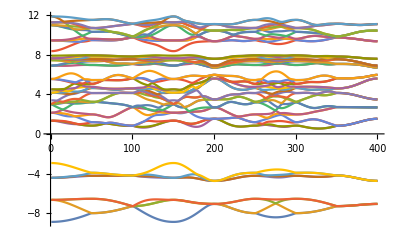

```mathematica
tr["ene"]//Transpose//ListLinePlot   (* the energy band *)
```

```mathematica
rep=getBandRep[205,"",tr];   (* get the LG IRs of each Bloch states *)
Keys[rep]
```

{kpath,rep,kinfo}

```mathematica
rep["kinfo"][[175]]
```

{{0.244898,0.244898,0.244898},Λ,ΓR,C3,{u,u,u},{E,{0,0,0}},{u,u,u},{0,0,0},u→0.244898,0.5,in G}

```mathematica
rep["kpath"]  (* the kpath of the energy band *)
```

[Γ(1)]-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-[X(50)]-[X(51)]-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-Z-[M(100)]-[M(101)]-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-[Γ(150)]-[Γ(151)]-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-Λ-[R(200)]-[R(201)]-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-[X(250)]-[X(251)]-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-UN-[X(300)]-[X(301)]-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-Z'-[M(350)]-[M(351)]-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-[R(400)]

```mathematica
(*  The LG IRs of the 175th k-point *)
rep["rep"][[175]]//TableForm[#,TableDepth->2]&
```

{1,1} | -8.23139 | 1 | {A,Λ_1(1)}
{2,2} | -6.94621 | 1 | {A,Λ_1(1)}
{3,4} | -6.91836 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{5,6} | -4.44257 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{7,7} | -4.07847 | 1 | {A,Λ_1(1)}
{8,8} | -3.86003 | 1 | {A,Λ_1(1)}
{9,9} | 0.734562 | 1 | {A,Λ_1(1)}
{10,11} | 1.03388 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{12,12} | 1.92745 | 1 | {A,Λ_1(1)}
{13,14} | 2.24187 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{15,15} | 2.44268 | 1 | {A,Λ_1(1)}
{16,17} | 3.11079 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{18,19} | 3.67673 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{20,20} | 4.28668 | 1 | {A,Λ_1(1)}
{21,22} | 4.50019 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{23,23} | 4.76332 | 1 | {A,Λ_1(1)}
{24,25} | 5.02326 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{26,26} | 5.18115 | 1 | {A,Λ_1(1)}
{27,28} | 5.87704 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{29,29} | 7.13229 | 1 | {A,Λ_1(1)}
{30,31} | 7.16032 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{32,32} | 7.2187 | 1 | {A,Λ_1(1)}
{33,34} | 7.26338 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{35,36} | 7.58204 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{37,37} | 7.68878 | 1 | {A,Λ_1(1)}
{38,39} | 7.72405 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{40,40} | 7.91995 | 1 | {A,Λ_1(1)}
{41,41} | 9.2078 | 1 | {A,Λ_1(1)}
{42,43} | 9.63749 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{44,44} | 9.83096 | 1 | {A,Λ_1(1)}
{45,45} | 10.028 | 1 | {A,Λ_1(1)}
{46,47} | 10.2576 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{48,49} | 10.7901 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}
{50,50} | 10.9931 | 1 | {A,Λ_1(1)}
{51,52} | 11.236 | 2 | {^2E⊕^1E,Λ_2(1)⊕Λ_3(1)}

```mathematica
showLGIrepTab[205,"Λ"]
```

No.205 PaOverBar[3]:  k-point name is Λ
BC standard:

  k_BC=(,,uuu) for ,,CubiPrim
Index |  |  |  | 1 | 2 | 3
Element |  |  |  | {E|000} | {C31+|000} | {C31-|000}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | 0 | 1
1 | 0 | 0
0 | 1 | 0) | (0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (1/2+ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | 1/2-ⅈ/2) | (1/2-ⅈ/2 | -1/2+ⅈ/2
1/2+ⅈ/2 | 1/2+ⅈ/2)
1 | Λ_1 | A | 1 | 1 | 1 | 1
2 | Λ_2 | ^2E | 3 | 1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3)
3 | Λ_3 | ^1E | 3 | 1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3)
4 | Λ_4 | ^1Ē | 3 | 1 | ⅇ^(-(ⅈ π)/3) | ⅇ^((ⅈ π)/3)
5 | Λ_5 | ^2Ē | 3 | 1 | ⅇ^((ⅈ π)/3) | ⅇ^(-(ⅈ π)/3)
6 | Λ_6 | Ā | 1 | 1 | -1 | -1

### For non - BC cells, take space group No. 186 for example (with SOC)

-Graphics-
The left cell is the cell used to do the VASP calculations, which is the idealized standard cell of spglib but not a BC cell.  The right cell is the BC cell. A conversion has to be done for the trace data before using getBandRep.

```mathematica
?convTraceToBC
```

convTraceToBC[sgno,traceData,P,p0,stdR]  converts traceData from non-BC standard to BC standard for getBandRep to determinate little group ireps. P, p0, and stdR are respectively dataset['transformation_matrix'], dataset['origin_shift'] and dataset['std_rotation_matrix'] from spglib acting on the initial cell. For non-SOC case stdR is not needed but for SOC case stdR has to be given.

```mathematica
trNonBC=readVasp2trace["SG186-trace.txt"];
trBC=convTraceToBC[186,trNonBC,IdentityMatrix[3],{0,0,0},IdentityMatrix[3]];
```

```mathematica
rep186=getBandRep[186,"",trBC];
```

```mathematica
rep186["kpath"]
```

[Γ(1)]-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-Σ-[M(21)]-[M(22)]-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-T'-[K(42)]-[K(43)]-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-T-[Γ(63)]-[Γ(64)]-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-Δ-[A(84)]-[A(85)]-R-R-R-R-R-R-R-R-R-R-R-R-R-R-R-R-R-R-R-[L(105)]-[L(106)]-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-S'-[H(126)]-[H(127)]-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-S-[A(147)]

```mathematica
rep186["rep"][[127]]//TableForm[#,TableDepth->2]&
```

{1,2} | -16.9095 | 2 | {Ē,H_6(2)}
{3,4} | -16.9074 | 2 | {Ē,H_6(2)}
{5,8} | -16.5424 | 4 | {2Ē,2H_6(2)}
{9,10} | -16.5275 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{11,12} | -16.5241 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{13,16} | -4.70922 | 4 | {(Ā)_1⊕(Ā)_2⊕Ē,H_4(1)⊕H_5(1)⊕H_6(2)}
{17,18} | 0.585097 | 2 | {Ē,H_6(2)}
{19,20} | 0.626712 | 2 | {Ē,H_6(2)}
{21,22} | 0.681115 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{23,24} | 0.772539 | 2 | {Ē,H_6(2)}
{25,26} | 0.853616 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{27,28} | 0.870083 | 2 | {Ē,H_6(2)}
{29,30} | 1.14083 | 2 | {Ē,H_6(2)}
{31,32} | 1.18022 | 2 | {Ē,H_6(2)}
{33,34} | 1.32426 | 2 | {Ē,H_6(2)}
{35,36} | 1.40065 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{37,38} | 1.76246 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{39,40} | 1.9626 | 2 | {Ē,H_6(2)}
{41,42} | 2.64197 | 2 | {Ē,H_6(2)}
{43,44} | 3.15371 | 2 | {Ē,H_6(2)}
{45,46} | 4.67307 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{47,48} | 4.88555 | 2 | {Ē,H_6(2)}
{49,50} | 7.25151 | 2 | {(Ā)_1⊕(Ā)_2,H_4(1)⊕H_5(1)}
{51,52} | 7.27258 | 2 | {Ē,H_6(2)}
{53,53} | 8.507 | 1 | {??,??}
{54,54} | 8.51504 | 1 | {??,??}
{55,55} | 8.55777 | 1 | {??,??}
{56,56} | 8.56821 | 1 | {??,??}

```mathematica
showLGCharTab[186,"H"]
```

No.186 P6_3mc:  k-point name is H
BC standard:

  k_BC=(,,-1/32/31/2) for ,,HexaPrim
Index |  |  |  | 1 | 2 | 3 | 4 | 5 | 6
Element |  |  |  | {E|000} | {C3+|000} | {C3-|000} | {σd1|001/2} | {σd2|001/2} | {σd3|001/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | -1 | 0
1 | -1 | 0
0 | 0 | 1) | (-1 | 1 | 0
-1 | 0 | 0
0 | 0 | 1) | (1 | -1 | 0
0 | -1 | 0
0 | 0 | 1) | (-1 | 0 | 0
-1 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (1/2+(ⅈ √3)/2 | 0
0 | 1/2-(ⅈ √3)/2) | (1/2-(ⅈ √3)/2 | 0
0 | 1/2+(ⅈ √3)/2) | (0 | -ⅈ
-ⅈ | 0) | (0 | ⅈ/2+(√3)/2
ⅈ/2-(√3)/2 | 0) | (0 | ⅈ/2-(√3)/2
ⅈ/2+(√3)/2 | 0)
1 | H_1 | ^1E_1 | 3 | 1 | 1 | 1 | ⅈ | ⅈ | ⅈ
2 | H_2 | ^2E_1 | 3 | 1 | 1 | 1 | -ⅈ | -ⅈ | -ⅈ
3 | H_3 | E_2 | 1 | 2 | -1 | -1 | 0 | 0 | 0
4 | H_4 | (Ā)_1 | 3 | 1 | -1 | -1 | 1 | 1 | 1
5 | H_5 | (Ā)_2 | 3 | 1 | -1 | -1 | -1 | -1 | -1
6 | H_6 | Ē | 2 | 2 | 1 | 1 | 0 | 0 | 0

## 7. Correspondence between BC and BCS conventions

### correspondence of k points

```mathematica
?showKptBCStoBC
```

showKptBCStoBC[sgno, BZtype]  shows correspondence between k points of BCS convention and BC convention in talbe form. BZtype is optional and is "a" by default.

```mathematica
showKptBCStoBC[38]
```

,   ,   No. 38Amm2BZ type (a)
BCS | BCSconv | BCSprim | BCStoBCprim | BC | BCprim | rot | gn
A | {1/2,0,w} | {1/2,w/2,w/2} | {-w/2,w/2,1/2} | B | {-α,α,1/2} | E | {0,0,0}
A | {1/2,0,w} | {1/2,w/2,w/2} | {-w/2,w/2,1/2} | G** | {1/2-α,1/2+α,1/2} | C2x | {-1,0,1}
GM | {0,0,0} | {0,0,0} | {0,0,0} | Γ | {0,0,0} | E | {0,0,0}
SM | {0,0,w} | {0,w/2,w/2} | {-w/2,w/2,0} | Δ | {-α,α,0} | E | {0,0,0}
SM | {0,0,w} | {0,w/2,w/2} | {-w/2,w/2,0} | F** | {1/2-α,1/2+α,0} | C2x | {-1,0,0}
T | {1/2,0,-1} | {1/2,-1/2,-1/2} | {1/2,-1/2,1/2} | T | {1/2,1/2,1/2} | E | {0,-1,0}
Y | {0,0,-1} | {0,-1/2,-1/2} | {1/2,-1/2,0} | Y | {1/2,1/2,0} | E | {0,-1,0}
Z | {1/2,0,0} | {1/2,0,0} | {0,0,1/2} | Z | {0,0,1/2} | E | {0,0,0}
B | {1/2,v,0} | {1/2,v/2,-v/2} | {v/2,v/2,1/2} | A | {α,α,1/2} | E | {0,0,0}
DT | {0,v,0} | {0,v/2,-v/2} | {v/2,v/2,0} | Σ | {α,α,0} | E | {0,0,0}
H | {u,0,-1} | {u,-1/2,-1/2} | {1/2,-1/2,u} | H | {1/2,1/2,α} | E | {0,-1,0}
LD | {u,0,0} | {u,0,0} | {0,0,u} | Λ | {0,0,α} | E | {0,0,0}
M | {u,0,w} | {u,w/2,w/2} | {-w/2,w/2,u} | UN |  |  | 
P | {0,v,w} | {0,(v+w)/2,1/2 (-v+w)} | {(v-w)/2,(v+w)/2,0} | UN |  |  | 
Q | {1/2,v,w} | {1/2,(v+w)/2,1/2 (-v+w)} | {(v-w)/2,(v+w)/2,1/2} | UN |  |  | 
R | {1/2,1/2,-1/2} | {1/2,0,-1/2} | {1/2,0,1/2} | R* | {0,1/2,1/2} | C2y | {1,0,1}
S | {0,1/2,-1/2} | {0,0,-1/2} | {1/2,0,0} | S* | {0,1/2,0} | C2y | {1,0,0}
D | {u,1/2,-1/2} | {u,0,-1/2} | {1/2,0,u} | D* | {0,1/2,α} | σx | {1,0,0}
GP | {u,v,w} | {u,(v+w)/2,1/2 (-v+w)} | {(v-w)/2,(v+w)/2,u} | GP |  |  | 
K | {u,v,0} | {u,v/2,-v/2} | {v/2,v/2,u} | GP |  |  |

-Graphics-
For details of Eq. (32), see our paper  arXiv:2012.08871.

```mathematica
showKptBCStoBC[38,"b"]
```

,   ,   No. 38Amm2BZ type (b)
BCS | BCSconv | BCSprim | BCStoBCprim | BC | BCprim | rot | gn
A | {1/2,0,w} | {1/2,w/2,w/2} | {-w/2,w/2,1/2} | B | {-α,α,1/2} | E | {0,0,0}
GM | {0,0,0} | {0,0,0} | {0,0,0} | Γ | {0,0,0} | E | {0,0,0}
SM | {0,0,w} | {0,w/2,w/2} | {-w/2,w/2,0} | Δ | {-α,α,0} | E | {0,0,0}
T | {1/2,0,-1} | {1/2,-1/2,-1/2} | {1/2,-1/2,1/2} | T | {-1/2,1/2,1/2} | E | {1,-1,0}
Y | {0,0,-1} | {0,-1/2,-1/2} | {1/2,-1/2,0} | Y | {-1/2,1/2,0} | E | {1,-1,0}
Z | {1/2,0,0} | {1/2,0,0} | {0,0,1/2} | Z | {0,0,1/2} | E | {0,0,0}
B | {1/2,v,0} | {1/2,v/2,-v/2} | {v/2,v/2,1/2} | A | {α,α,1/2} | E | {0,0,0}
B | {1/2,v,0} | {1/2,v/2,-v/2} | {v/2,v/2,1/2} | E* | {-1/2+α,1/2+α,1/2} | C2y | {1,0,1}
DT | {0,v,0} | {0,v/2,-v/2} | {v/2,v/2,0} | Σ | {α,α,0} | E | {0,0,0}
DT | {0,v,0} | {0,v/2,-v/2} | {v/2,v/2,0} | C* | {-1/2+α,1/2+α,0} | C2y | {1,0,0}
H | {u,0,-1} | {u,-1/2,-1/2} | {1/2,-1/2,u} | H | {-1/2,1/2,α} | E | {1,-1,0}
LD | {u,0,0} | {u,0,0} | {0,0,u} | Λ | {0,0,α} | E | {0,0,0}
M | {u,0,w} | {u,w/2,w/2} | {-w/2,w/2,u} | UN |  |  | 
P | {0,v,w} | {0,(v+w)/2,1/2 (-v+w)} | {(v-w)/2,(v+w)/2,0} | UN |  |  | 
Q | {1/2,v,w} | {1/2,(v+w)/2,1/2 (-v+w)} | {(v-w)/2,(v+w)/2,1/2} | UN |  |  | 
R | {1/2,1/2,-1/2} | {1/2,0,-1/2} | {1/2,0,1/2} | R* | {0,1/2,1/2} | C2y | {1,0,1}
S | {0,1/2,-1/2} | {0,0,-1/2} | {1/2,0,0} | S* | {0,1/2,0} | C2y | {1,0,0}
D | {u,1/2,-1/2} | {u,0,-1/2} | {1/2,0,u} | D* | {0,1/2,α} | σx | {1,0,0}
GP | {u,v,w} | {u,(v+w)/2,1/2 (-v+w)} | {(v-w)/2,(v+w)/2,u} | GP |  |  | 
K | {u,v,0} | {u,v/2,-v/2} | {v/2,v/2,u} | GP |  |  |

### correspondence of LG IRs

```mathematica
?showKrepBCStoBC
```

showKrepBCStoBC[sgno, BZtype]  shows correspondence between little-gorup ireps of BCS convention and BC convention in talbe form. BZtype is optional and is "a" by default. For double space group the option "DSG"->True is needed.

```mathematica
showKrepBCStoBC[38]
showKrepBCStoBC[38,"DSG"->True]
```

No. 38 | Amm2 | BZ type (a)
A1 | 1 | B_1 | A_1 | x
A2 | 1 | B_3 | A_2 | x
A3 | 1 | B_2 | B_1 | x
A4 | 1 | B_4 | B_2 | x
SM1 | 1 | Δ_1 | A_1 | x
SM2 | 1 | Δ_3 | A_2 | x
SM3 | 1 | Δ_2 | B_1 | x
SM4 | 1 | Δ_4 | B_2 | x
Y1 | 1 | Y_1 | A_1 | 1
Y2 | 1 | Y_3 | A_2 | 1
Y3 | 1 | Y_2 | B_1 | 1
Y4 | 1 | Y_4 | B_2 | 1
H1 | 1 | H_1 | A' | 1
H2 | 1 | H_2 | A'' | 1
P1 | 1 | UN_1 | A' | x
P2 | 1 | UN_2 | A'' | x
S1 | 1 | S_1 | A' | 1
S2 | 1 | S_2 | A'' | 1 | A1 | 1 | G_1 | A_1 | x
A2 | 1 | G_3 | A_2 | x
A3 | 1 | G_2 | B_1 | x
A4 | 1 | G_4 | B_2 | x
SM1 | 1 | F_1 | A_1 | x
SM2 | 1 | F_3 | A_2 | x
SM3 | 1 | F_2 | B_1 | x
SM4 | 1 | F_4 | B_2 | x
Z1 | 1 | Z_1 | A_1 | 1
Z2 | 1 | Z_3 | A_2 | 1
Z3 | 1 | Z_2 | B_1 | 1
Z4 | 1 | Z_4 | B_2 | 1
LD1 | 1 | Λ_1 | A' | 1
LD2 | 1 | Λ_2 | A'' | 1
Q1 | 1 | UN_1 | A' | x
Q2 | 1 | UN_2 | A'' | x
D1 | 1 | D_1 | A | 1
K1 | 1 | GP_1 | A | 1 | GM1 | 1 | Γ_1 | A_1 | 1
GM2 | 1 | Γ_3 | A_2 | 1
GM3 | 1 | Γ_2 | B_1 | 1
GM4 | 1 | Γ_4 | B_2 | 1
T1 | 1 | T_1 | A_1 | 1
T2 | 1 | T_3 | A_2 | 1
T3 | 1 | T_2 | B_1 | 1
T4 | 1 | T_4 | B_2 | 1
B1 | 1 | A_1 | A' | 1
B2 | 1 | A_2 | A'' | 1
DT1 | 1 | Σ_1 | A' | 1
DT2 | 1 | Σ_2 | A'' | 1
M1 | 1 | UN_1 | A' | x
M2 | 1 | UN_2 | A'' | x
R1 | 1 | R_1 | A' | 1
R2 | 1 | R_2 | A'' | 1
GP1 | 1 | GP_1 | A | x

No. 38 (double) | Amm2 | BZ type (a)
-A5 | 2 | B_5 | Ē | x
-SM5 | 2 | Δ_5 | Ē | x
-Y5 | 2 | Y_5 | Ē | 2
-DT3 | 1 | Σ_4 | ^1Ē | 2
-DT4 | 1 | Σ_3 | ^2Ē | 2
-M3 | 1 | UN_3 | ^2Ē | x
-M4 | 1 | UN_4 | ^1Ē | x
-R3 | 1 | R_3 | ^2Ē | 3
-R4 | 1 | R_4 | ^1Ē | 3
-GP2 | 1 | GP_2 | Ā | x | -A5 | 2 | G_5 | Ē | x
-SM5 | 2 | F_5 | Ē | x
-Z5 | 2 | Z_5 | Ē | 2
-H3 | 1 | H_3 | ^2Ē | 2
-H4 | 1 | H_4 | ^1Ē | 2
-P3 | 1 | UN_4 | ^1Ē | x
-P4 | 1 | UN_3 | ^2Ē | x
-S3 | 1 | S_3 | ^2Ē | 3
-S4 | 1 | S_4 | ^1Ē | 3
-K2 | 1 | GP_2 | Ā | 2 | -GM5 | 2 | Γ_5 | Ē | 2
-T5 | 2 | T_5 | Ē | 2
-B3 | 1 | A_4 | ^1Ē | 2
-B4 | 1 | A_3 | ^2Ē | 2
-LD3 | 1 | Λ_3 | ^2Ē | 2
-LD4 | 1 | Λ_4 | ^1Ē | 2
-Q3 | 1 | UN_4 | ^1Ē | x
-Q4 | 1 | UN_3 | ^2Ē | x
-D2 | 1 | D_2 | Ā | 2

-Graphics-

```mathematica
showKrepBCStoBC[38,"b"]
showKrepBCStoBC[38,"b","DSG"->True]
```

No. 38 | Amm2 | BZ type (b)
A1 | 1 | B_1 | A_1 | x
A2 | 1 | B_3 | A_2 | x
A3 | 1 | B_2 | B_1 | x
A4 | 1 | B_4 | B_2 | x
T1 | 1 | T_1 | A_1 | 1
T2 | 1 | T_3 | A_2 | 1
T3 | 1 | T_2 | B_1 | 1
T4 | 1 | T_4 | B_2 | 1
B1 | 1 | A_1 | A' | 1
B2 | 1 | A_2 | A'' | 1
DT1 | 1 | C_1 | A' | 1
DT2 | 1 | C_2 | A'' | 1
M1 | 1 | UN_1 | A' | x
M2 | 1 | UN_2 | A'' | x
R1 | 1 | R_1 | A' | 1
R2 | 1 | R_2 | A'' | 1
K1 | 1 | GP_1 | A | 1 | GM1 | 1 | Γ_1 | A_1 | 1
GM2 | 1 | Γ_3 | A_2 | 1
GM3 | 1 | Γ_2 | B_1 | 1
GM4 | 1 | Γ_4 | B_2 | 1
Y1 | 1 | Y_1 | A_1 | 1
Y2 | 1 | Y_3 | A_2 | 1
Y3 | 1 | Y_2 | B_1 | 1
Y4 | 1 | Y_4 | B_2 | 1
B1 | 1 | E_1 | A' | 1
B2 | 1 | E_2 | A'' | 1
H1 | 1 | H_1 | A' | 1
H2 | 1 | H_2 | A'' | 1
P1 | 1 | UN_1 | A' | x
P2 | 1 | UN_2 | A'' | x
S1 | 1 | S_1 | A' | 1
S2 | 1 | S_2 | A'' | 1 | SM1 | 1 | Δ_1 | A_1 | x
SM2 | 1 | Δ_3 | A_2 | x
SM3 | 1 | Δ_2 | B_1 | x
SM4 | 1 | Δ_4 | B_2 | x
Z1 | 1 | Z_1 | A_1 | 1
Z2 | 1 | Z_3 | A_2 | 1
Z3 | 1 | Z_2 | B_1 | 1
Z4 | 1 | Z_4 | B_2 | 1
DT1 | 1 | Σ_1 | A' | 1
DT2 | 1 | Σ_2 | A'' | 1
LD1 | 1 | Λ_1 | A' | 1
LD2 | 1 | Λ_2 | A'' | 1
Q1 | 1 | UN_1 | A' | x
Q2 | 1 | UN_2 | A'' | x
D1 | 1 | D_1 | A | 1
GP1 | 1 | GP_1 | A | x

No. 38 (double) | Amm2 | BZ type (b)
-A5 | 2 | B_5 | Ē | x
-T5 | 2 | T_5 | Ē | 2
-B3 | 1 | A_4 | ^1Ē | 2
-B4 | 1 | A_3 | ^2Ē | 2
-DT3 | 1 | C_3 | ^2Ē | 2
-DT4 | 1 | C_4 | ^1Ē | 2
-M3 | 1 | UN_3 | ^2Ē | x
-M4 | 1 | UN_4 | ^1Ē | x
-R3 | 1 | R_3 | ^2Ē | 3
-R4 | 1 | R_4 | ^1Ē | 3
-K2 | 1 | GP_2 | Ā | 2 | -GM5 | 2 | Γ_5 | Ē | 2
-Y5 | 2 | Y_5 | Ē | 2
-B3 | 1 | E_3 | ^2Ē | 2
-B4 | 1 | E_4 | ^1Ē | 2
-H3 | 1 | H_3 | ^2Ē | 2
-H4 | 1 | H_4 | ^1Ē | 2
-P3 | 1 | UN_4 | ^1Ē | x
-P4 | 1 | UN_3 | ^2Ē | x
-S3 | 1 | S_3 | ^2Ē | 3
-S4 | 1 | S_4 | ^1Ē | 3 | -SM5 | 2 | Δ_5 | Ē | x
-Z5 | 2 | Z_5 | Ē | 2
-DT3 | 1 | Σ_4 | ^1Ē | 2
-DT4 | 1 | Σ_3 | ^2Ē | 2
-LD3 | 1 | Λ_3 | ^2Ē | 2
-LD4 | 1 | Λ_4 | ^1Ē | 2
-Q3 | 1 | UN_4 | ^1Ē | x
-Q4 | 1 | UN_3 | ^2Ē | x
-D2 | 1 | D_2 | Ā | 2
-GP2 | 1 | GP_2 | Ā | x

## End

For more details, please refer to the  paper  arXiv : 2012.08871.
https://doi.org/10.1016/j.cpc.2021.107993